```mathematica
N[Solve[1-x1-x2/(1+x2) -x3/(1+x3) - x4/(1+x4)==0&&1-x2-x1/(1+x1) - x3/(1+x3)- x4/(1+x4)==0&&1-x3-x1/(1+x1) - x2/(1+x2)- x4/(1+x4)==0&&1-x3/(1+x3)-x1/(1+x1) - x2/(1+x2) - x4== 0, {x1, x2, x3, x4}]]
```

{{x1→-0.5,x2→1.,x3→1.,x4→1.},{x1→1.,x2→1.,x3→-0.5,x4→1.},{x1→1.,x2→1.,x3→1.,x4→-0.5},{x1→1.,x2→-0.5,x3→1.,x4→1.},{x1→-0.5-0.866025 ⅈ,x2→-0.5+0.866025 ⅈ,x3→-0.5-0.866025 ⅈ,x4→-0.5+0.866025 ⅈ},{x1→-0.5-0.866025 ⅈ,x2→-0.5+0.866025 ⅈ,x3→-0.5+0.866025 ⅈ,x4→-0.5-0.866025 ⅈ},{x1→-0.5-0.866025 ⅈ,x2→-0.5-0.866025 ⅈ,x3→-0.5+0.866025 ⅈ,x4→-0.5+0.866025 ⅈ},{x1→-0.5+0.866025 ⅈ,x2→-0.5-2.59808 ⅈ,x3→-0.5+0.866025 ⅈ,x4→-0.5+0.866025 ⅈ},{x1→-0.5+0.866025 ⅈ,x2→-0.5-0.866025 ⅈ,x3→-0.5+0.866025 ⅈ,x4→-0.5-0.866025 ⅈ},{x1→-0.5+0.866025 ⅈ,x2→-0.0540541+0.324324 ⅈ,x3→-0.5-0.866025 ⅈ,x4→-0.945946-0.324324 ⅈ},{x1→-3.30278,x2→-3.30278,x3→-3.30278,x4→-3.30278},{x1→0.302776,x2→0.302776,x3→0.302776,x4→0.302776}}

```mathematica
ContourPlot[{2+5*x1-x2/(1+x2)==0,2+5*x2-x1/(1+x1)==0 }, {x1, -5, 5}, {x2, -5, 5}];
```

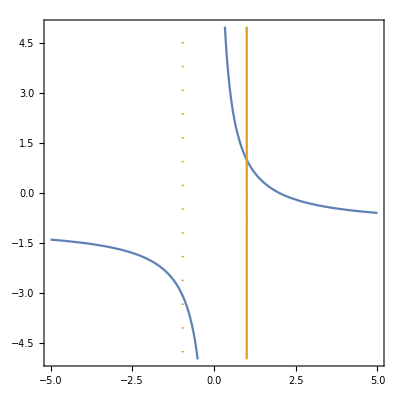

```mathematica
ContourPlot[{1-a11*x1+2*(a11-1)*x2/(1+x2)==0,1-(1-2*a11)*x2-4*a11*x1/(1+x1)==0}, {x1, -5, 5}, {x2, -5, 5}]
```

```mathematica
a11 = a11;
N[Solve[1-a11*x1+2*(a11-1)*x2/(1+x2)==0&&1-(1-2*a11)*x2-4*a11*x1/(1+x1)==0 {x1, x2}]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x1→1.,x2→1.}}

```mathematica
FullSimplify[Solve[1-a11*x1+a12*x2/(1+x2)==0, {x2}][[1]][[1]][[2]]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
(-2.+x1)/(2.+2. a12-1. x1)
```

(-2.+x1)/(2.+2. a12-1. x1)

# Imposing tangency on a feasible planted equilibrium

```mathematica
Clear[a11];
eq1 = 1 - a11*x1 + a12*x2/(1 + x2) + a13*x3/(1+x3);
eq2 = 1 - a22*x2 - a21*x1/(1 + x1)+ a23*x3/(1+x3);eq3 = 1 - a33*x3 - a31*x1/(1 + x1)+ a32*x2/(1+x2);
```

```mathematica
constr1 = eq1/.x1-> 1/.x2->1 /.x3->1 ;
constr2 = eq2/.x1-> 1/.x2->1/.x3->1 ;
constr3 = eq3/.x1-> 1/.x2->1/.x3->1;
```

```mathematica
curve1 = Solve[eq1==0, x3][[1]][[1]][[2]];
curve2 = Solve[eq2==0, x3][[1]][[1]][[2]];
curve2 = Solve[eq2==0, x3][[1]][[1]][[2]];
```

(1+x1-a21 x1-a22 x2-a22 x1 x2)/(-1-a23-x1+a21 x1-a23 x1+a22 x2+a22 x1 x2)

```mathematica
derivative1 = D[curve1, x1]/.x1->1/.x2->1/.x3->1;
```

```mathematica
derivative2 = D[curve2, x1]/.x1->1/.x2->1/.x3->1;
```

```mathematica
Solve[constr1 == 0 && constr2 ==0&& derivative1==derivative2, {a12, a21, a22}]
```

{{a12→2 (-1+a11),a21→(8 a11)/(1+3 a11),a22→(1-a11)/(1+3 a11)}}

```mathematica
eq1constr = eq1/.a12->2 (-1+a11) +RandomReal[{-0.1, 0.1}]/.a21->(8 a11)/(1+3 a11)+RandomReal[{-0.1, 0.1}]/.a22->(1-a11)/(1+3 a11)+RandomReal[{-0.1, 0.1}];
eq2constr = eq2/.a12->2 (-1+a11)+RandomReal[{-0.1, 0.1}]/.a21->(8 a11)/(1+3 a11)+RandomReal[{-0.1, 0.1}]/.a22->(1-a11)/(1+3 a11)+RandomReal[{-0.1, 0.1}];
```

```mathematica
a11 = 0.5;
Solve[eq1constr==0&&eq2constr==0, {x1, x2}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x1→0.822035,x2→1.44715},{x1→1.99238,x2→0.00383864}}

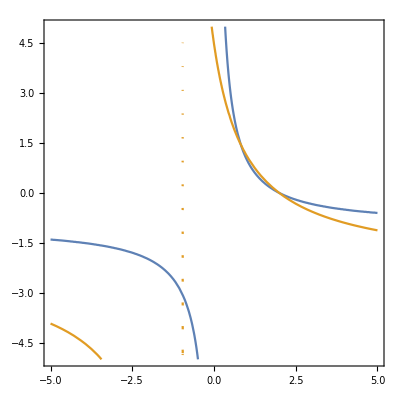

```mathematica
ContourPlot[{eq1constr, eq2constr}, {x1, -5, 5}, {x2, -5, 5}]
```

```mathematica
FullSimplify[n+1/2*n*(n-1)]
```

1/2 n (1+n)

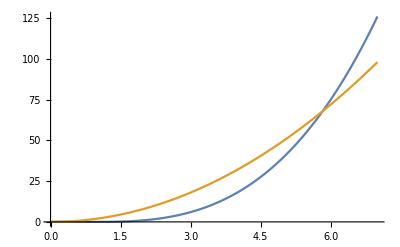

```mathematica
1/2 n (1+n)
Plot[{Binomial[n, 2]*(n-1), 2*n^2}, {n, 0, 7}]
```

## Putting glv with functional responses in polynomial form

```mathematica
Clear[a11]
eq1 = (1+x2)*(1+x3)*(r1 - a11*x1)+ x2*a12*(1+x3) + x3*a13*(1+x2);
MonomialList[eq1, {x1, x2, x3}]
```

{-a11 x1 x2 x3,-a11 x1 x2,-a11 x1 x3,-a11 x1,(a12+a13+r1) x2 x3,(a12+r1) x2,(a13+r1) x3,r1}

### Bidirectional mutualism in C-R

```mathematica
eq1 =(h2+x2)*(h3+x3)*(e1+x1)*(r1 - a11*x1) + a12*x2*(h3+x3)*(e1+x1) + a13*x3*(h2+x2)*(e1+x1)-(b31*x3 + b21*x2)*(h2+x2)*(h3+x3);
eq2 = (h1+x1)*(h3+x3)*(e2+x2)*(r2-a22*x2) + a21*x1*(h3+x3)*(e2+x2) + a23*x3*(h1+x1)*(e2+x2) - (b12*x1 + b32*x3)*(h1+x1)*(h3+x3);
eq3 = (h1+x1)*(h2+x2)*(e3+x3)*(r3-a33*x3) + a31*x1*(e3 + x3)*(h2+x2)+  a32*x2*(h1+x1)*(e3+x3)-(b13*x1+b32*x2)*(h1 + x1)*(h2+x2);
```

```mathematica
MonomialList[{eq1, eq2, eq3}, {x1, x2, x3}, "DegreeLexicographic"]
```

{{-a11 x1^2 x2 x3,-a11 h3 x1^2 x2,-a11 h2 x1^2 x3,(a12+a13-a11 e1+r1) x1 x2 x3,-b21 x2^2 x3,-b31 x2 x3^2,-a11 h2 h3 x1^2,(a12 h3-a11 e1 h3+h3 r1) x1 x2,(a13 h2-a11 e1 h2+h2 r1) x1 x3,-b21 h3 x2^2,(a12 e1+a13 e1-b21 h2-b31 h3+e1 r1) x2 x3,-b31 h2 x3^2,(-a11 e1 h2 h3+h2 h3 r1) x1,(a12 e1 h3-b21 h2 h3+e1 h3 r1) x2,(a13 e1 h2-b31 h2 h3+e1 h2 r1) x3,e1 h2 h3 r1},{-a22 x1 x2^2 x3,-b12 x1^2 x3,-a22 h3 x1 x2^2,(a21+a23-a22 e2+r2) x1 x2 x3,-b32 x1 x3^2,-a22 h1 x2^2 x3,-b12 h3 x1^2,(a21 h3-a22 e2 h3+h3 r2) x1 x2,(a21 e2+a23 e2-b12 h1-b32 h3+e2 r2) x1 x3,-a22 h1 h3 x2^2,(a23 h1-a22 e2 h1+h1 r2) x2 x3,-b32 h1 x3^2,(a21 e2 h3-b12 h1 h3+e2 h3 r2) x1,(-a22 e2 h1 h3+h1 h3 r2) x2,(a23 e2 h1-b32 h1 h3+e2 h1 r2) x3,e2 h1 h3 r2},{-a33 x1 x2 x3^2,-b13 x1^2 x2,-b32 x1 x2^2,(a31+a32-a33 e3+r3) x1 x2 x3,-a33 h2 x1 x3^2,-a33 h1 x2 x3^2,-b13 h2 x1^2,(a31 e3+a32 e3-b13 h1-b32 h2+e3 r3) x1 x2,(a31 h2-a33 e3 h2+h2 r3) x1 x3,-b32 h1 x2^2,(a32 h1-a33 e3 h1+h1 r3) x2 x3,-a33 h1 h2 x3^2,(a31 e3 h2-b13 h1 h2+e3 h2 r3) x1,(a32 e3 h1-b32 h1 h2+e3 h1 r3) x2,(-a33 e3 h1 h2+h1 h2 r3) x3,e3 h1 h2 r3}}

```mathematica
r1 = r2 =r3= 0.3;
a21 = a12 = 0.6;
a31=a13=0.6;
a32=a23=0.6;
q1 = q2 = 1;
b21 = b12 = 0.2;
b31 = b13 = 0.2;
b32 = b23 = 0.2;
c1 = c2 = 1;
a11=a22=a33 =0.01;
h1=h2=h3=0.3;
e1=e2=e3=0.3;
```

```mathematica
Solve[eq1==0&&eq2==0&&eq3==0, {x1, x2,x3}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x1→-0.3,x3→-0.3},{x1→-0.3,x2→-0.3},{x2→-0.3,x3→-0.3},{x1→-0.3,x2→-0.145023,x3→-0.3},{x1→0.375127,x2→-0.145023,x3→0.375127},{x1→-0.3,x2→-0.0819807,x3→-0.3},{x1→-0.0819807,x2→-0.0819807,x3→-0.0819807},{x1→-0.3,x2→-0.0626546,x3→-0.3},{x1→-0.0626546,x2→-0.0626546,x3→0.737623},{x1→0.737623,x2→-0.0626546,x3→-0.0626546},{x1→-0.3,x2→0.375127,x3→-0.3},{x1→-0.145023,x2→0.375127,x3→0.375127},{x1→0.375127,x2→0.375127,x3→-0.145023},{x1→-0.3,x2→0.737623,x3→-0.3},{x1→-0.0626546,x2→0.737623,x3→-0.0626546},{x1→-0.3,x2→1.2,x3→-0.3},{x1→-0.3,x2→27.3038,x3→-0.3},{x1→27.3038,x2→27.3038,x3→140.965},{x1→140.965,x2→27.3038,x3→27.3038},{x1→-0.3,x2→47.2428,x3→-0.3},{x1→121.784,x2→47.2428,x3→121.784},{x1→-0.3,x2→109.782,x3→-0.3},{x1→109.782,x2→109.782,x3→109.782},{x1→-0.3,x2→121.784,x3→-0.3},{x1→47.2428,x2→121.784,x3→121.784},{x1→121.784,x2→121.784,x3→47.2428},{x1→-0.3,x2→140.965,x3→-0.3},{x1→27.3038,x2→140.965,x3→27.3038}}

```mathematica
StreamPlot[{eq1, eq2},{x1, 0, 100}, {x2,0, 100}]
```

-Graphics-

### Mary’s suggestion

```mathematica
Clear[A]
f1=r-A*x1+B*(x2/(h+x2)+x3/(h+x3)+x4/(h+x4))-G/(k+x1)*(x2+x3+x4);
f2=r-A*x2+B*(x1/(h+x1)+x3/(h+x3)+x4/(h+x4))-G/(k+x2)*(x1+x3+x4);
f3=r-A*x3+B*(x2/(h+x2)+x1/(h+x1)+x4/(h+x4))-G/(k+x3)*(x2+x1+x4);
f4=r-A*x4+B*(x2/(h+x2)+x3/(h+x3)+x1/(h+x1))-G/(k+x4)*(x2+x3+x1);
```

```mathematica
h=k=1;
B=G=1;
A =1.01;
r=A;
```

```mathematica
soln = Solve[f1==0&&f2==0&&f3==0&&f4==0&&x1>0&&x2>0&&x3>0&&x4>0, {x1, x2, x3, x4}, Reals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x1→0.0220555,x2→0.0220555,x3→1.02112,x4→1.02112},{x1→0.0220555,x2→1.02112,x3→0.0220555,x4→1.02112},{x1→0.0220555,x2→1.02112,x3→1.02112,x4→0.0220555},{x1→0.759416,x2→0.759416,x3→1.1578,x4→1.1578},{x1→0.759416,x2→1.1578,x3→0.759416,x4→1.1578},{x1→0.759416,x2→1.1578,x3→1.1578,x4→0.759416},{x1→0.970229,x2→1.00954,x3→1.00954,x4→1.00954},{x1→1.,x2→1.,x3→1.,x4→1.},{x1→1.00954,x2→1.00954,x3→1.00954,x4→0.970229},{x1→1.00954,x2→0.970229,x3→1.00954,x4→1.00954},{x1→1.00954,x2→1.00954,x3→0.970229,x4→1.00954},{x1→1.02112,x2→0.0220555,x3→1.02112,x4→0.0220555},{x1→1.02112,x2→1.02112,x3→0.0220555,x4→0.0220555},{x1→1.02112,x2→0.0220555,x3→0.0220555,x4→1.02112},{x1→1.1578,x2→0.759416,x3→1.1578,x4→0.759416},{x1→1.1578,x2→1.1578,x3→0.759416,x4→0.759416},{x1→1.1578,x2→0.759416,x3→0.759416,x4→1.1578}}

```mathematica
J = {{D[f1, x1]/.{x1->1, x2->1, x3->1, x4->1},D[f1, x2]/.{x1->1, x2->1, x3->1, x4->1}, D[f1, x3]/.{x1->1, x2->1, x3->1, x4->1}, D[f1, x4]/.{x1->1, x2->1, x3->1, x4->1} }, {D[f2, x1]/.{x1->1, x2->1, x3->1, x4->1},D[f2, x2]/.{x1->1, x2->1, x3->1, x4->1}, D[f2, x3]/.{x1->1, x2->1, x3->1, x4->1}, D[f2, x4]/.{x1->1, x2->1, x3->1, x4->1}}, {D[f3, x1]/.{x1->1, x2->1, x3->1, x4->1},D[f3, x2]/.{x1->1, x2->1, x3->1, x4->1}, D[f3, x3]/.{x1->1, x2->1, x3->1, x4->1}, D[f3, x4]/.{x1->1, x2->1, x3->1, x4->1}}, {D[f4, x1]/.{x1->1, x2->1, x3->1, x4->1},D[f4, x2]/.{x1->1, x2->1, x3->1, x4->1}, D[f4, x3]/.{x1->1, x2->1, x3->1, x4->1}, D[f4, x4]/.{x1->1, x2->1, x3->1, x4->1}}}
```

{{-0.26,-1/4,-1/4,-1/4},{-1/4,-0.26,-1/4,-1/4},{-1/4,-1/4,-0.26,-1/4},{-1/4,-1/4,-1/4,-0.26}}

```mathematica
Eigenvalues[J]
```

{-1.01,-0.01,-0.01,-0.01}

```mathematica
{1-A,1-A,1-A,-A}
(*This means that the equilibrium (1,1,1,1) is stable when A > 1, and unstable when A < 1*)
```

### Beverton-Holt model

```mathematica
eq1 = a*x1^2/(1 + x1^2) - x1;
eq2 = b*x2^2/(1+x2^2) - x2;
eq3= c*x3^2/(1+x3^2) - x3;
a = 2.5;
b =c = a;
```

```mathematica
N[Solve[eq1==0&&eq2==0&&eq3==0&&x1>0&&x2>0&&x3>0,{x1, x2, x3}, Reals]]
```

{{x1→0.101021,x2→0.101021,x3→0.101021},{x1→9.89898,x2→0.101021,x3→0.101021},{x1→0.101021,x2→9.89898,x3→0.101021},{x1→9.89898,x2→9.89898,x3→0.101021},{x1→0.101021,x2→0.101021,x3→9.89898},{x1→9.89898,x2→0.101021,x3→9.89898},{x1→0.101021,x2→9.89898,x3→9.89898},{x1→9.89898,x2→9.89898,x3→9.89898}}

### Competitive Beverton-Holt model (as in Brett and Kulenović, 2014, p. 2)

```mathematica
eq1 = a*x1^2/(1 + x1^2 + c*x2) - x1;
eq2 = b*x2^2/(1+x2^2+ d*x1) - x2;
a = 2.5;
b = 2.2;
c=0.13;
d =0.09;
```

```mathematica
N[Solve[eq1==0&&eq2==0,{x1, x2}]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x1→0.5,x2→0.},{x1→0.563425,x2→0.700886},{x1→0.642719,x2→1.49007},{x1→1.87702,x2→1.30265},{x1→1.91684,x2→0.90639},{x1→2.,x2→0.},{x1→0.,x2→0.},{x1→0.,x2→0.641742},{x1→0.,x2→1.55826}}

### Now with 3 species...

```mathematica
eq1 = a*x1^2/(1 + x1^2 + b*x2 + b*x3) - x1;
eq2 = a*x2^2/(1+x2^2+ b*x1 + b*x3) - x2;
eq3 = a*x3^2/(1+x3^2+ b*x1+ b*x2) - x3
a = 4;
b = 0.627;
NSolve[{eq1==0, eq2==0, eq3==0,x1>0, x2>0, x3>0}, {x1, x2, x3}]
```

-x3+(4 x3^2)/(1+0.627 x1+0.627 x2+x3^2)

{{x1→1.68556,x2→1.68556,x3→2.94144},{x1→1.68556,x2→2.94144,x3→1.68556},{x1→2.94144,x2→1.68556,x3→1.68556},{x1→2.31444,x2→2.31256,x3→2.31444},{x1→2.31256,x2→2.31444,x3→2.31444},{x1→2.31444,x2→2.31444,x3→2.31256},{x1→2.31381,x2→2.31381,x3→2.31381},{x1→0.432187,x2→0.432187,x3→0.432187}}

```mathematica
N[Solve[eq1==0&&eq2==0&&eq3==0,{x1, x2, x3}]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x1→0.5,x2→0.,x3→0.},{x1→0.549213,x2→0.549213,x3→0.},{x1→0.597625-0.0969635 ⅈ,x2→0.,x3→1.12546-0.973178 ⅈ},{x1→0.597625+0.0969635 ⅈ,x2→0.,x3→1.12546+0.973178 ⅈ},{x1→0.655305-0.133694 ⅈ,x2→0.655305-0.133694 ⅈ,x3→1.08863-1.08949 ⅈ},{x1→0.655305+0.133694 ⅈ,x2→0.655305+0.133694 ⅈ,x3→1.08863+1.08949 ⅈ},{x1→0.692646,x2→1.93735,x3→0.},{x1→0.794986-0.162277 ⅈ,x2→1.83501+0.162277 ⅈ,x3→1.10188-1.29825 ⅈ},{x1→0.794986+0.162277 ⅈ,x2→1.83501-0.162277 ⅈ,x3→1.10188+1.29825 ⅈ},{x1→1.71469-0.2446 ⅈ,x2→1.71469-0.2446 ⅈ,x3→1.41137+1.99329 ⅈ},{x1→1.71469+0.2446 ⅈ,x2→1.71469+0.2446 ⅈ,x3→1.41137-1.99329 ⅈ},{x1→1.82079,x2→1.82079,x3→0.},{x1→1.83501-0.254647 ⅈ,x2→0.794986+0.254647 ⅈ,x3→1.39812+2.03723 ⅈ},{x1→1.83501+0.254647 ⅈ,x2→0.794986-0.254647 ⅈ,x3→1.39812-2.03723 ⅈ},{x1→1.90237-0.20441 ⅈ,x2→0.,x3→1.37454+2.05157 ⅈ},{x1→1.90237+0.20441 ⅈ,x2→0.,x3→1.37454-2.05157 ⅈ},{x1→1.93735,x2→0.692646,x3→0.},{x1→2.,x2→0.,x3→0.},{x1→0.,x2→0.5,x3→0.},{x1→0.,x2→0.549213,x3→0.549213},{x1→0.,x2→0.692646,x3→1.93735},{x1→0.,x2→1.82079,x3→1.82079},{x1→0.,x2→1.93735,x3→0.692646},{x1→0.,x2→2.,x3→0.},{x1→0.,x2→0.,x3→0.},{x1→0.,x2→0.,x3→0.5},{x1→0.,x2→0.,x3→2.}}

#### A cell regulatory network

```mathematica
eq1 = k11*x1^n/(theta11^n + x1^n)+k12*x2^n/(theta12^n + x2^n)-k1*x1;
```

```mathematica
eq2 = k21*x1^n/(theta21^n + x1^n)+k22*x2^n/(theta22^n + x2^n)-k2*x2;
```

```mathematica
k11 = k22 = 2;
k12 = k21 = 3;
k1 = k2 = 1;
theta11 = theta22 = 1;
theta12 = theta21 = 2;
n=20;
```

StreamPlot::pllim: Range specification eq2 is not of the form {x, xmin, xmax}.

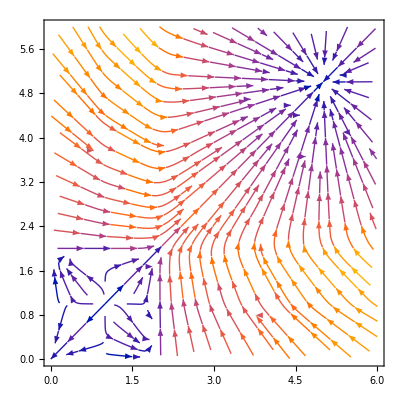

```mathematica
StreamPlot[{eq1,eq2},{x1, 0, 6},{x2, 0, 6}]
```

```mathematica
Solve[eq1==0&&eq2==0, {x1, x2}]
```

```mathematica
J = {{a, b, b, b}, {b, a, b, b}, {b, b, a, b}, {b, b, b, a}}
```

{{a,b,b,b},{b,a,b,b},{b,b,a,b},{b,b,b,a}}

```mathematica
Eigenvectors[J]
```

{{-1,0,0,1},{-1,0,1,0},{-1,1,0,0},{1,1,1,1}}

### GLV competitive with type II functional response

```mathematica
fun[A_, x_, i_, n_] := 1- x[[i]] -Sum[A[[i,j]]*x[[j]]/(1+x[[j]]), {j, DeleteCases[Range[1,n],i]}];
```

```mathematica
n = 3;
A = Array[Subscript[a,#1,#2]&,{n,n}]
X = Array[Subscript[x,#1]&,n] 
fun[A, X, 1, n]
```

{{a_(1,1),a_(1,2),a_(1,3)},{a_(2,1),a_(2,2),a_(2,3)},{a_(3,1),a_(3,2),a_(3,3)}}

{x_1,x_2,x_3}

1-x_1-(x_2 a_(1,2))/(1+x_2)-(x_3 a_(1,3))/(1+x_3)

```mathematica
n=4;
A = ConstantArray[1.5, {n, n}];(*ResourceFunction["RandomMatrix"][Real,{0,0.1},{n,n}];*)
X =Array[Subscript[x,#1]&,n] ;  
Solve[{ fun[A, X, 1, n]==0, fun[A, X, 2, n]==0, fun[A, X, 3, n]==0,  fun[A, X, 4, n]==0}, X]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x_1→-4.71221,x_2→-4.71221,x_3→-4.71221,x_4→-4.71221},{x_1→0.,x_2→0.,x_3→0.5,x_4→0.5},{x_1→0.,x_2→0.5,x_3→0.,x_4→0.5},{x_1→0.,x_2→0.5,x_3→0.5,x_4→0.},{x_1→0.2,x_2→0.2,x_3→0.2,x_4→0.25},{x_1→0.2,x_2→0.2,x_3→0.25,x_4→0.2},{x_1→0.2,x_2→0.25,x_3→0.2,x_4→0.2},{x_1→0.212214,x_2→0.212214,x_3→0.212214,x_4→0.212214},{x_1→0.25,x_2→0.2,x_3→0.2,x_4→0.2},{x_1→0.5,x_2→0.,x_3→0.,x_4→0.5},{x_1→0.5,x_2→0.,x_3→0.5,x_4→0.},{x_1→0.5,x_2→0.5,x_3→0.,x_4→0.}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x_1→-4.71221,x_2→-4.71221,x_3→-4.71221,x_4→-4.71221},{x_1→0.,x_2→0.,x_3→0.5,x_4→0.5},{x_1→0.,x_2→0.5,x_3→0.,x_4→0.5},{x_1→0.,x_2→0.5,x_3→0.5,x_4→0.},{x_1→0.2,x_2→0.2,x_3→0.2,x_4→0.25},{x_1→0.2,x_2→0.2,x_3→0.25,x_4→0.2},{x_1→0.2,x_2→0.25,x_3→0.2,x_4→0.2},{x_1→0.212214,x_2→0.212214,x_3→0.212214,x_4→0.212214},{x_1→0.25,x_2→0.2,x_3→0.2,x_4→0.2},{x_1→0.5,x_2→0.,x_3→0.,x_4→0.5},{x_1→0.5,x_2→0.,x_3→0.5,x_4→0.},{x_1→0.5,x_2→0.5,x_3→0.,x_4→0.}}

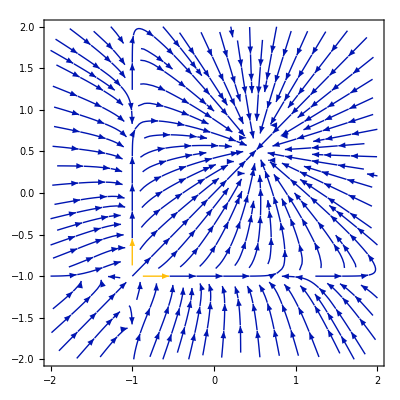

```mathematica
StreamPlot[{fun[A,S, R, X, 1, n],fun[A, S,R, X, 2, n]}, {Subscript[x, 1], -2, 2}, {Subscript[x, 2], -2, 2}]
```

```mathematica
fun[A,S, R, X, 1, n]
```

Part::partd1: Depth of object {0.9,0.9} is not sufficient for the given part specification.

Part::partd: Part specification {0.9,0.9}⟦1,1⟧ is longer than depth of object.

0.5-{0.9,0.9}⟦1,1⟧ x_1-(0.0852691 x_1)/(1+x_1)-(0.145633 x_2)/(1+x_2)

### Symmetric case

```mathematica
eq1 = 1 - x1 - δ*x2/(1+x2) - δ*x3/(1+x3); 
eq2 = 1 - x2 - δ*x1/(1+x1) - δ*x3/(1+x3);
eq3 = 1 - x3 - δ*x1/(1+x1) - δ*x2/(1+x2);
symeq1 = FullSimplify[eq1/.x1->x/.x2->x/.x3->x]
```

1+x (-1-(2 δ)/(1+x))

```mathematica
Solve[symeq1==0,x ]
```

{{x→-δ-√(1+δ^2)},{x→-δ+√(1+δ^2)}}

```mathematica
eq1sym = eq1/.x1->y/.x2->z/.x3->z;
eq2sym =eq3/.x1->y/.x2->z/.x3->z;
FullSimplify[Solve[{eq1sym==0,eq2sym==0}, {y, z}]]
```

{{y→-3+2 δ,z→-(-2+δ)/(2 (-1+δ))},{y→-δ-√(1+δ^2),z→-δ-√(1+δ^2)},{y→-δ+√(1+δ^2),z→-δ+√(1+δ^2)}}

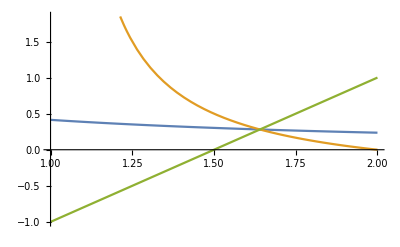

```mathematica
Plot[{-δ+√(1+δ^2),-(-2+δ)/(2 (-1+δ)), -3+2 δ}, {δ, 1, 2}]
```

```mathematica
alpha = D[eq1, x1]/.x1->x/.x2->x/.x3->x
beta = D[eq1, x2]/.x1->x/.x2->x/.x3->x
eig = (alpha - beta)/.x->-δ+√(1+δ^2)
deltac = NSolve[eig==0, δ][[1]][[1]][[2]]
```

1-2 x-(2 x δ)/(1+x)

x ((x δ)/(1+x)^2-δ/(1+x))

1-2 (-δ+√(1+δ^2))-(2 δ (-δ+√(1+δ^2)))/(1-δ+√(1+δ^2))-(-δ+√(1+δ^2)) ((δ (-δ+√(1+δ^2)))/((1-δ+√(1+δ^2))^2)-δ/(1-δ+√(1+δ^2)))

1.64039

```mathematica
neq1 = eq1/.δ->deltac;
neq2 = eq2/.δ->deltac;
neq3 = eq3/.δ->deltac;
Solve[{neq1==0, neq2==0, neq3==0, x1>0, x2>0, x3>0}, {x1, x2, x3}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x1→0.280776,x2→0.280776,x3→0.280776},{x1→0.280776,x2→0.280776,x3→0.280776},{x1→0.280776,x2→0.280776,x3→0.280776},{x1→0.280776,x2→0.280776,x3→0.280776}}

```mathematica
neq1 = eq1/.δ->deltac+0.1;
neq2 = eq2/.δ->deltac+0.1;
neq3 = eq3/.δ->deltac+0.1;
Solve[{neq1==0, neq2==0, neq3==0, x1>0, x2>0, x3>0}, {x1, x2, x3}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x1→0.175321,x2→0.175321,x3→0.480776},{x1→0.175321,x2→0.480776,x3→0.175321},{x1→0.266837,x2→0.266837,x3→0.266837},{x1→0.480776,x2→0.175321,x3→0.175321}}

### Sparse interactions (n)

```mathematica
fun[A_,R_ ,x_, i_, n_] := R- x[[i]] -Sum[A[[i,j]]*x[[j]]/(1+x[[j]]), {j, DeleteCases[Range[1,n],i]}];
```

{{x→-2 a-√(1+4 a^2)},{x→-2 a+√(1+4 a^2)}}

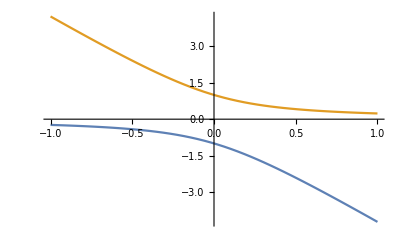

-2 a+√(1+4 a^2)

```mathematica
n=5;
A = {{a, a, a, a,a}, {a, a, a, a, a}, {a, a, a, a, a}, {a, a, a, a, a}, {a, a, a, a, a}};(*ResourceFunction["RandomMatrix"][Real,{0,0.1},{n,n}];*)
X =Array[Subscript[x,#1]&,n] ;  
R = 1;
eq1 = fun[A, R,X, 1, n];
eq2 = fun[A,R, X, 2, n];
eq3 = fun[A,R, X, 3, n];
eq4 = fun[A, R,X, 4, n];
eq5 = fun[A,R, X, 5, n];
symeq1 = FullSimplify[eq1/.X[[1]]->x/.X[[2]]->x/.X[[3]]->x/.X[[4]]->x/. X[[5]]->x];
sols = Solve[symeq1==0, x]
Plot[{sols[[1]][[1]][[2]], sols[[2]][[1]][[2]]}, {a, -1, 1}]
xsym = sols[[2]][[1]][[2]]
```

```mathematica
J11 =FullSimplify[ D[eq1, X[[1]]]/.X[[1]]->x/.X[[2]]->x/.X[[3]]->x/.X[[4]]->x/.X[[5]]->x]
J12 = FullSimplify[D[eq1,X[[2]]]/.X[[1]]->x/.X[[2]]->x/.X[[3]]->x/.X[[4]]->x/.X[[5]]->x]
J13 =FullSimplify [D[eq1, X[[3]]]/.X[[1]]->x/.X[[2]]->x/.X[[3]]->x/.X[[4]]->x/.X[[5]]->x]
J14 =FullSimplify [D[eq1, X[[4]]]/.X[[1]]->x/.X[[2]]->x/.X[[3]]->x/.X[[4]]->x/.X[[5]]->x]
J15 =FullSimplify [D[eq1, X[[5]]]/.X[[1]]->x/.X[[2]]->x/.X[[3]]->x/.X[[4]]->x/.X[[5]]->x]
```

-1

-a/(1+x)^2

-a/(1+x)^2

-a/(1+x)^2

«1 more identical outputs»

```mathematica
J = {{-1,J12,J12,J12,  J12}, {J12, -1, J12, J12, J12}, {J12, J12, -1, J12, J12}, {J12,J12, J12, -1, J12},  {J12, J12, J12, J12, -1}}/.x->xsym;
eig1 = FullSimplify[Eigenvalues[J][[2]]]
acrit = NSolve[eig1==0, a][[1]][[1]][[2]]
```

1/((1-2 a+√(1+4 a^2))^2)Root[512-5120 a+27840 a^2-105440 a^3+302370 a^4-679680 a^5+1209480 a^6-1687040 a^7+1781760 a^8-1310720 a^9+524288 a^10+512 √(1+4 a^2)-5120 a √(1+4 a^2)+26816 a^2 √(1+4 a^2)-95200 a^3 √(1+4 a^2)+249762 a^4 √(1+4 a^2)-499524 a^5 √(1+4 a^2)+761600 a^6 √(1+4 a^2)-858112 a^7 √(1+4 a^2)+655360 a^8 √(1+4 a^2)-262144 a^9 √(1+4 a^2)+(640-5120 a+22800 a^2-70640 a^3+162545 a^4-282560 a^5+364800 a^6-327680 a^7+163840 a^8+640 √(1+4 a^2)-5120 a √(1+4 a^2)+21520 a^2 √(1+4 a^2)-60400 a^3 √(1+4 a^2)+120800 a^4 √(1+4 a^2)-172160 a^5 √(1+4 a^2)+163840 a^6 √(1+4 a^2)-81920 a^7 √(1+4 a^2)) #1+(320-1920 a+6660 a^2-15860 a^3+26640 a^4-30720 a^5+20480 a^6+320 √(1+4 a^2)-1920 a √(1+4 a^2)+6020 a^2 √(1+4 a^2)-12040 a^3 √(1+4 a^2)+15360 a^4 √(1+4 a^2)-10240 a^5 √(1+4 a^2)) #1^2+(80-320 a+790 a^2-1280 a^3+1280 a^4+80 √(1+4 a^2)-320 a √(1+4 a^2)+640 a^2 √(1+4 a^2)-640 a^3 √(1+4 a^2)) #1^3+(10-20 a+40 a^2+10 √(1+4 a^2)-20 a √(1+4 a^2)) #1^4+#1^5&,2]

1.38154

```mathematica
neq1 = eq1/.a->acrit;
neq2 = eq2/.a->acrit;
neq3 = eq3/.a->acrit;
neq4 = eq4/.a->acrit;
neq5 = eq5/.a-> acrit;
```

```mathematica
NSolve[{neq1==0,neq2==0,neq3==0,neq4==0, neq5==0 }, X]
```

{{x_1→-5.70156,x_3→-5.70156,x_2→-5.70156,x_4→-5.70156,x_5→-5.70156},{x_1→1.35078,x_3→1.35078,x_2→-0.412305,x_4→1.35078,x_5→-0.412305},{x_1→-0.412305,x_3→1.35078,x_2→1.35078,x_4→-0.412305,x_5→1.35078},{x_1→-0.412305,x_3→-0.412305,x_2→1.35078,x_4→1.35078,x_5→1.35078},{x_1→1.35078,x_3→-0.412305,x_2→1.35078,x_4→1.35078,x_5→-0.412305},{x_1→-0.412305,x_3→1.35078,x_2→-0.412305,x_4→1.35078,x_5→1.35078},{x_1→1.35078,x_3→-0.412305,x_2→-0.412305,x_4→1.35078,x_5→1.35078},{x_1→1.35078,x_3→1.35078,x_2→-0.412305,x_4→-0.412305,x_5→1.35078},{x_1→1.35078,x_3→-0.412305,x_2→1.35078,x_4→-0.412305,x_5→1.35078},{x_1→1.35078,x_3→1.35078,x_2→1.35078,x_4→-0.412305,x_5→-0.412305},{x_1→-0.412305,x_3→1.35078,x_2→1.35078,x_4→1.35078,x_5→-0.412305},{x_1→0.175391-7.01441×10^-10 ⅈ,x_3→0.175391+1.96028×10^-10 ⅈ,x_2→0.17539-3.34672×10^-9 ⅈ,x_4→0.175391+7.07946×10^-10 ⅈ,x_5→0.17539+3.14418×10^-9 ⅈ},{x_1→0.175391+2.80184×10^-7 ⅈ,x_3→0.175391-9.95191×10^-8 ⅈ,x_2→0.175391-1.31991×10^-7 ⅈ,x_4→0.175391-1.05471×10^-7 ⅈ,x_5→0.17539+5.67976×10^-8 ⅈ},{x_1→0.175391-2.56361×10^-7 ⅈ,x_3→0.175391+7.43164×10^-8 ⅈ,x_2→0.175391+1.18162×10^-7 ⅈ,x_4→0.175391+8.30888×10^-8 ⅈ,x_5→0.17539-1.92065×10^-8 ⅈ},{x_1→0.175391-5.77033×10^-9 ⅈ,x_3→0.17539+1.30308×10^-9 ⅈ,x_2→0.175391+1.32308×10^-9 ⅈ,x_4→0.175391-8.61089×10^-10 ⅈ,x_5→0.17539+4.00526×10^-9 ⅈ},{x_1→0.175391-4.91357×10^-9 ⅈ,x_3→0.175391-9.0751×10^-10 ⅈ,x_2→0.175391+1.66461×10^-9 ⅈ,x_4→0.17539+4.98074×10^-10 ⅈ,x_5→0.17539+3.65839×10^-9 ⅈ},{x_1→0.17539+5.2761×10^-9 ⅈ,x_3→0.17539+1.08759×10^-9 ⅈ,x_2→0.17539-1.74657×10^-9 ⅈ,x_4→0.175391-6.13447×10^-10 ⅈ,x_5→0.175391-4.00367×10^-9 ⅈ},{x_1→0.17539+5.32576×10^-9 ⅈ,x_3→0.175391-1.2124×10^-9 ⅈ,x_2→0.17539-1.18632×10^-9 ⅈ,x_4→0.17539+8.34074×10^-10 ⅈ,x_5→0.175391-3.76111×10^-9 ⅈ},{x_1→0.175391+5.72061×10^-10 ⅈ,x_3→0.17539-1.28579×10^-10 ⅈ,x_2→0.175391+2.56005×10^-9 ⅈ,x_4→0.17539-5.27119×10^-10 ⅈ,x_5→0.175391-2.47641×10^-9 ⅈ},{x_1→0.175391-2.51743×10^-7 ⅈ,x_3→0.17539+9.01553×10^-8 ⅈ,x_2→0.17539+1.18449×10^-7 ⅈ,x_4→0.17539+9.51188×10^-8 ⅈ,x_5→0.175391-5.19808×10^-8 ⅈ},{x_1→0.175391+2.71834×10^-7 ⅈ,x_3→0.17539-7.93426×10^-8 ⅈ,x_2→0.17539-1.24836×10^-7 ⅈ,x_4→0.17539-8.89342×10^-8 ⅈ,x_5→0.175391+2.12784×10^-8 ⅈ},{x_1→0.175391-1.67149×10^-7 ⅈ,x_3→0.175391+1.07884×10^-7 ⅈ,x_2→0.175391-1.19019×10^-7 ⅈ,x_4→0.175391+1.09366×10^-7 ⅈ,x_5→0.175391+6.89186×10^-8 ⅈ},{x_1→0.175391+1.72196×10^-7 ⅈ,x_3→0.175391-1.04524×10^-7 ⅈ,x_2→0.175391-1.17703×10^-7 ⅈ,x_4→0.175391+1.06892×10^-7 ⅈ,x_5→0.175391-5.68594×10^-8 ⅈ},{x_1→0.175391+1.59096×10^-7 ⅈ,x_3→0.175391+9.54325×10^-8 ⅈ,x_2→0.175391-1.08078×10^-7 ⅈ,x_4→0.175391-9.74607×10^-8 ⅈ,x_5→0.175391-4.89897×10^-8 ⅈ},{x_1→0.175391-1.88093×10^-7 ⅈ,x_3→0.175391-1.12429×10^-7 ⅈ,x_2→0.175391+1.27592×10^-7 ⅈ,x_4→0.175391+1.15504×10^-7 ⅈ,x_5→0.175391+5.7426×10^-8 ⅈ},{x_1→0.175391+1.68282×10^-7 ⅈ,x_3→0.175391-1.08305×10^-7 ⅈ,x_2→0.175391+1.20134×10^-7 ⅈ,x_4→0.175391-1.10452×10^-7 ⅈ,x_5→0.175391-6.96606×10^-8 ⅈ},{x_1→0.175391-1.60922×10^-7 ⅈ,x_3→0.175391+9.75982×10^-8 ⅈ,x_2→0.175391+1.10159×10^-7 ⅈ,x_4→0.175391-1.00202×10^-7 ⅈ,x_5→0.175391+5.33678×10^-8 ⅈ}}

```mathematica
neq1 = eq1/.a->(acrit+0.01);
neq2 = eq2/.a->(acrit+0.01);
neq3 = eq3/.a->(acrit+0.01);
neq4 = eq4/.a->(acrit+0.01);
neq5 = eq5/.a-> (acrit+0.01);
NSolve[{neq1==0,neq2==0,neq3==0,neq4==0, neq5==0}, X]
```

{{x_1→-5.74038,x_3→-5.74038,x_2→-5.74038,x_4→-5.74038,x_5→-5.74038},{x_1→1.41262,x_3→1.41262,x_2→-0.423223,x_4→-0.423223,x_5→1.41262},{x_1→-0.423223,x_3→1.41262,x_2→1.41262,x_4→1.41262,x_5→-0.423223},{x_1→-0.423223,x_3→-0.423223,x_2→1.41262,x_4→1.41262,x_5→1.41262},{x_1→1.41262,x_3→-0.423223,x_2→-0.423223,x_4→1.41262,x_5→1.41262},{x_1→1.41262,x_3→-0.423223,x_2→1.41262,x_4→1.41262,x_5→-0.423223},{x_1→1.41262,x_3→-0.423223,x_2→1.41262,x_4→-0.423223,x_5→1.41262},{x_1→1.41262,x_3→1.41262,x_2→-0.423223,x_4→1.41262,x_5→-0.423223},{x_1→1.41262,x_3→1.41262,x_2→1.41262,x_4→-0.423223,x_5→-0.423223},{x_1→-0.423223,x_3→1.41262,x_2→-0.423223,x_4→1.41262,x_5→1.41262},{x_1→-0.423223,x_3→1.41262,x_2→1.41262,x_4→-0.423223,x_5→1.41262},{x_1→0.206308,x_3→0.153555,x_2→0.206308,x_4→0.153555,x_5→0.153555},{x_1→0.153555,x_3→0.153555,x_2→0.153555,x_4→0.206308,x_5→0.206308},{x_1→0.153555,x_3→0.206308,x_2→0.153555,x_4→0.206308,x_5→0.153555},{x_1→0.153555,x_3→0.206308,x_2→0.206308,x_4→0.153555,x_5→0.153555},{x_1→0.153555,x_3→0.206308,x_2→0.153555,x_4→0.153555,x_5→0.206308},{x_1→0.153555,x_3→0.153555,x_2→0.206308,x_4→0.206308,x_5→0.153555},{x_1→0.206308,x_3→0.153555,x_2→0.153555,x_4→0.153555,x_5→0.206308},{x_1→0.206308,x_3→0.153555,x_2→0.153555,x_4→0.206308,x_5→0.153555},{x_1→0.206308,x_3→0.206308,x_2→0.153555,x_4→0.153555,x_5→0.153555},{x_1→0.153555,x_3→0.153555,x_2→0.206308,x_4→0.153555,x_5→0.206308},{x_1→0.170619,x_3→0.170619,x_2→0.170619,x_4→0.170619,x_5→0.188724},{x_1→0.170619,x_3→0.170619,x_2→0.170619,x_4→0.188724,x_5→0.170619},{x_1→0.170619,x_3→0.170619,x_2→0.188724,x_4→0.170619,x_5→0.170619},{x_1→0.170619,x_3→0.188724,x_2→0.170619,x_4→0.170619,x_5→0.170619},{x_1→0.188724,x_3→0.170619,x_2→0.170619,x_4→0.170619,x_5→0.170619},{x_1→0.174205,x_3→0.174205,x_2→0.174205,x_4→0.174205,x_5→0.174205}}

### Sparse interactions (n-1)

```mathematica
fun[A_, x_, i_, n_] := 1- x[[i]] -Sum[A[[i,j]]*x[[j]]/(1+x[[j]]), {j, DeleteCases[Range[1,n],i]}];
```

1-x_1-(a x_2)/(1+x_2)-(a x_3)/(1+x_3)-(a x_4)/(1+x_4)

1+x (-1-(3 a)/(1+x))

{{x→1/2 (-3 a-√(4+9 a^2))},{x→1/2 (-3 a+√(4+9 a^2))}}

1/2 (-3 a+√(4+9 a^2))

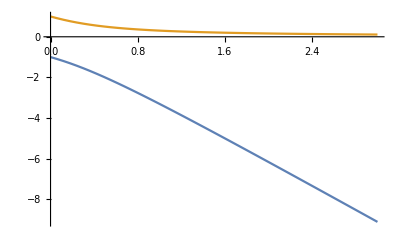

```mathematica
n=5;
γ = 0;
A = {{0, a, a, a,γ*a}, {γ*a, 0, a, a, a}, {a, γ*a, 0, a, a}, {a, a, γ*a, 0, a}, {a, a, a, γ*a, 0}};(*ResourceFunction["RandomMatrix"][Real,{0,0.1},{n,n}];*)
X =Array[Subscript[x,#1]&,n] ;  
eq1 = fun[A, X, 1, n]
eq2 = fun[A, X, 2, n];
eq3 = fun[A, X, 3, n];
eq4 = fun[A, X, 4, n];
eq5 = fun[A, X, 5, n];
symeq1 = FullSimplify[eq1/.X[[1]]->x/.X[[2]]->x/.X[[3]]->x/.X[[4]]->x/. X[[5]]->x]
sols = Solve[symeq1==0, x]
xsym = sols[[2]][[1]][[2]]
Plot[{sols[[1]][[1]][[2]], sols[[2]][[1]][[2]]}, {a, 0, 3}]
```

```mathematica
J11 =FullSimplify[ D[eq1, X[[1]]]/.X[[1]]->xsym/.X[[2]]->xsym/.X[[3]]->xsym/.X[[4]]->xsym/.X[[5]]->xsym]
J12 = FullSimplify[D[eq1,X[[2]]]/.X[[1]]->xsym/.X[[2]]->xsym/.X[[3]]->xsym/.X[[4]]->xsym/.X[[5]]->xsym]
J13 =FullSimplify [D[eq1, X[[3]]]/.X[[1]]->xsym/.X[[2]]->xsym/.X[[3]]->xsym/.X[[4]]->xsym/.X[[5]]->xsym]
J14 =FullSimplify [D[eq1, X[[4]]]/.X[[1]]->xsym/.X[[2]]->xsym/.X[[3]]->xsym/.X[[4]]->xsym/.X[[5]]->xsym]
J15 =FullSimplify [D[eq1, X[[5]]]/.X[[1]]->xsym/.X[[2]]->xsym/.X[[3]]->xsym/.X[[4]]->xsym/.X[[5]]->xsym]
```

-1

-(4 a)/((2-3 a+√(4+9 a^2))^2)

-(4 a)/((2-3 a+√(4+9 a^2))^2)

-(4 a)/((2-3 a+√(4+9 a^2))^2)

0

```mathematica
J = {{-1, J12, J12,J12,  J15}, {J15, -1, J12, J12,J12}, {J12, J15, -1, J12, J12}, {J12, J12, J15, -1, J12},  {J12, J12, J12,J15, -1}};
eig1 = FullSimplify[Eigenvalues[J][[5]]]
acrit =NSolve[eig1==0, a][[1]][[1]][[2]]
```

1/((2-3 a+√(4+9 a^2))^2)Root[524288-3932160 a+16056320 a^2-45629440 a^3+98170880 a^4-165519360 a^5+220884480 a^6-230999040 a^7+182891520 a^8-100776960 a^9+30233088 a^10+262144 √(4+9 a^2)-1966080 a √(4+9 a^2)+7733248 a^2 √(4+9 a^2)-20602880 a^3 √(4+9 a^2)+40551424 a^4 √(4+9 a^2)-60827136 a^5 √(4+9 a^2)+69534720 a^6 √(4+9 a^2)-58724352 a^7 √(4+9 a^2)+33592320 a^8 √(4+9 a^2)-10077696 a^9 √(4+9 a^2)+(163840-983040 a+3287040 a^2-7639040 a^3+13185280 a^4-17187840 a^5+16640640 a^6-11197440 a^7+4199040 a^8+81920 √(4+9 a^2)-491520 a √(4+9 a^2)+1551360 a^2 √(4+9 a^2)-3266560 a^3 √(4+9 a^2)+4899840 a^4 √(4+9 a^2)-5235840 a^5 √(4+9 a^2)+3732480 a^6 √(4+9 a^2)-1399680 a^7 √(4+9 a^2)) #1+(20480-92160 a+240000 a^2-428480 a^3+540000 a^4-466560 a^5+233280 a^6+10240 √(4+9 a^2)-46080 a √(4+9 a^2)+108480 a^2 √(4+9 a^2)-162720 a^3 √(4+9 a^2)+155520 a^4 √(4+9 a^2)-77760 a^5 √(4+9 a^2)) #1^2+(1280-3840 a+7120 a^2-8640 a^3+6480 a^4+640 √(4+9 a^2)-1920 a √(4+9 a^2)+2880 a^2 √(4+9 a^2)-2160 a^3 √(4+9 a^2)) #1^3+(40-60 a+90 a^2+20 √(4+9 a^2)-30 a √(4+9 a^2)) #1^4+#1^5&,5]

0.921695-0.446899 ⅈ

```mathematica
neq1 = eq1/.a->acrit;
neq2 = eq2/.a->acrit;
neq3 = eq3/.a->acrit;
neq4 = eq4/.a->acrit;
neq5 = eq5/.a-> acrit;
sols/.a->acrit
```

{{x→-3.04745+1.22701 ⅈ},{x→0.282367+0.11369 ⅈ}}

```mathematica
NSolve[{neq1==0,neq2==0,neq3==0,neq4==0, neq5==0}, X]
```

{{x_1→-1.08667-0.496504 ⅈ,x_2→-1.17634-4.95023 ⅈ,x_3→-0.844383+0.271264 ⅈ,x_4→-1.12868-0.780738 ⅈ,x_5→-0.895517+0.216279 ⅈ},{x_1→-1.12868-0.780738 ⅈ,x_2→-0.895517+0.216279 ⅈ,x_3→-1.08667-0.496504 ⅈ,x_4→-1.17634-4.95023 ⅈ,x_5→-0.844383+0.271264 ⅈ},{x_1→-1.17634-4.95023 ⅈ,x_2→-0.844383+0.271264 ⅈ,x_3→-1.12868-0.780738 ⅈ,x_4→-0.895517+0.216279 ⅈ,x_5→-1.08667-0.496504 ⅈ},{x_1→-0.844383+0.271264 ⅈ,x_2→-1.12868-0.780738 ⅈ,x_3→-0.895517+0.216279 ⅈ,x_4→-1.08667-0.496504 ⅈ,x_5→-1.17634-4.95023 ⅈ},{x_1→-0.895517+0.216279 ⅈ,x_2→-1.08667-0.496504 ⅈ,x_3→-1.17634-4.95023 ⅈ,x_4→-0.844383+0.271264 ⅈ,x_5→-1.12868-0.780738 ⅈ},{x_1→-3.04745+1.22701 ⅈ,x_2→-3.04745+1.22701 ⅈ,x_3→-3.04745+1.22701 ⅈ,x_4→-3.04745+1.22701 ⅈ,x_5→-3.04745+1.22701 ⅈ},{x_1→-0.772754-0.704516 ⅈ,x_2→-0.736079+0.575918 ⅈ,x_3→-0.964618-0.437108 ⅈ,x_4→-0.842009+0.387744 ⅈ,x_5→0.341821+2.73651 ⅈ},{x_1→0.341821+2.73651 ⅈ,x_2→-0.772754-0.704516 ⅈ,x_3→-0.736079+0.575918 ⅈ,x_4→-0.964618-0.437108 ⅈ,x_5→-0.842009+0.387744 ⅈ},{x_1→-0.736079+0.575918 ⅈ,x_2→-0.964618-0.437108 ⅈ,x_3→-0.842009+0.387744 ⅈ,x_4→0.341821+2.73651 ⅈ,x_5→-0.772754-0.704516 ⅈ},{x_1→-0.842009+0.387744 ⅈ,x_2→0.341821+2.73651 ⅈ,x_3→-0.772754-0.704516 ⅈ,x_4→-0.736079+0.575918 ⅈ,x_5→-0.964618-0.437108 ⅈ},{x_1→-0.964618-0.437108 ⅈ,x_2→-0.842009+0.387744 ⅈ,x_3→0.341821+2.73651 ⅈ,x_4→-0.772754-0.704516 ⅈ,x_5→-0.736079+0.575918 ⅈ},{x_1→-0.889896-1.04876 ⅈ,x_2→-0.519409-2.50059 ⅈ,x_3→-0.665962+0.346845 ⅈ,x_4→-0.40053+1.35855 ⅈ,x_5→-0.352399+0.465616 ⅈ},{x_1→-0.665962+0.346845 ⅈ,x_2→-0.40053+1.35855 ⅈ,x_3→-0.352399+0.465616 ⅈ,x_4→-0.889896-1.04876 ⅈ,x_5→-0.519409-2.50059 ⅈ},{x_1→-0.519409-2.50059 ⅈ,x_2→-0.665962+0.346845 ⅈ,x_3→-0.40053+1.35855 ⅈ,x_4→-0.352399+0.465616 ⅈ,x_5→-0.889896-1.04876 ⅈ},{x_1→-0.352399+0.465616 ⅈ,x_2→-0.889896-1.04876 ⅈ,x_3→-0.519409-2.50059 ⅈ,x_4→-0.665962+0.346845 ⅈ,x_5→-0.40053+1.35855 ⅈ},{x_1→-0.40053+1.35855 ⅈ,x_2→-0.352399+0.465616 ⅈ,x_3→-0.889896-1.04876 ⅈ,x_4→-0.519409-2.50059 ⅈ,x_5→-0.665962+0.346845 ⅈ},{x_1→0.284714+0.114068 ⅈ,x_2→0.283453+0.111577 ⅈ,x_3→0.280693+0.112002 ⅈ,x_4→0.280243+0.114764 ⅈ,x_5→0.282734+0.116041 ⅈ},{x_1→0.282927+0.115959 ⅈ,x_2→0.284696+0.113859 ⅈ,x_3→0.283249+0.11153 ⅈ,x_4→0.280584+0.112182 ⅈ,x_5→0.28038+0.114923 ⅈ},{x_1→0.280837+0.112148 ⅈ,x_2→0.280426+0.114672 ⅈ,x_3→0.282703+0.115839 ⅈ,x_4→0.284512+0.114035 ⅈ,x_5→0.283359+0.111759 ⅈ},{x_1→0.283243+0.111679 ⅈ,x_2→0.280725+0.112234 ⅈ,x_3→0.280474+0.114805 ⅈ,x_4→0.282844+0.115834 ⅈ,x_5→0.284551+0.113899 ⅈ},{x_1→0.280499+0.114674 ⅈ,x_2→0.282728+0.115771 ⅈ,x_3→0.284455+0.11399 ⅈ,x_4→0.283299+0.111799 ⅈ,x_5→0.280856+0.112218 ⅈ},{x_1→0.280798+0.112318 ⅈ,x_2→0.280576+0.114761 ⅈ,x_3→0.282834+0.115724 ⅈ,x_4→0.284443+0.113875 ⅈ,x_5→0.283186+0.111775 ⅈ}}

```mathematica
dacrit = acrit + 0.01;
```

```mathematica
neq1 = eq1/.a->dacrit;
neq2 = eq2/.a->dacrit;
neq3 = eq3/.a->dacrit;
neq4 = eq4/.a->dacrit;
neq5 = eq5/.a->dacrit;
NSolve[{neq1==0,neq2==0,neq3==0,neq4==0, neq5==0 }, X]
```

{{x_1→-1.12647-0.784698 ⅈ,x_2→-0.894298+0.217165 ⅈ,x_3→-1.08539-0.499001 ⅈ,x_4→-1.14527-4.96736 ⅈ,x_5→-0.842293+0.272004 ⅈ},{x_1→-0.842293+0.272004 ⅈ,x_2→-1.12647-0.784698 ⅈ,x_3→-0.894298+0.217165 ⅈ,x_4→-1.08539-0.499001 ⅈ,x_5→-1.14527-4.96736 ⅈ},{x_1→-1.08539-0.499001 ⅈ,x_2→-1.14527-4.96736 ⅈ,x_3→-0.842293+0.272004 ⅈ,x_4→-1.12647-0.784698 ⅈ,x_5→-0.894298+0.217165 ⅈ},{x_1→-1.14527-4.96736 ⅈ,x_2→-0.842293+0.272004 ⅈ,x_3→-1.12647-0.784698 ⅈ,x_4→-0.894298+0.217165 ⅈ,x_5→-1.08539-0.499001 ⅈ},{x_1→-0.894298+0.217165 ⅈ,x_2→-1.08539-0.499001 ⅈ,x_3→-1.14527-4.96736 ⅈ,x_4→-0.842293+0.272004 ⅈ,x_5→-1.12647-0.784698 ⅈ},{x_1→-3.07548+1.22868 ⅈ,x_2→-3.07548+1.22868 ⅈ,x_3→-3.07548+1.22868 ⅈ,x_4→-3.07548+1.22868 ⅈ,x_5→-3.07548+1.22868 ⅈ},{x_1→-0.840673+0.390687 ⅈ,x_2→0.359861+2.7492 ⅈ,x_3→-0.764486-0.699018 ⅈ,x_4→-0.733305+0.580775 ⅈ,x_5→-0.96048-0.437314 ⅈ},{x_1→-0.764486-0.699018 ⅈ,x_2→-0.733305+0.580775 ⅈ,x_3→-0.96048-0.437314 ⅈ,x_4→-0.840673+0.390687 ⅈ,x_5→0.359861+2.7492 ⅈ},{x_1→0.359861+2.7492 ⅈ,x_2→-0.764486-0.699018 ⅈ,x_3→-0.733305+0.580775 ⅈ,x_4→-0.96048-0.437314 ⅈ,x_5→-0.840673+0.390687 ⅈ},{x_1→-0.733305+0.580775 ⅈ,x_2→-0.96048-0.437314 ⅈ,x_3→-0.840673+0.390687 ⅈ,x_4→0.359861+2.7492 ⅈ,x_5→-0.764486-0.699018 ⅈ},{x_1→-0.96048-0.437314 ⅈ,x_2→-0.840673+0.390687 ⅈ,x_3→0.359861+2.7492 ⅈ,x_4→-0.764486-0.699018 ⅈ,x_5→-0.733305+0.580775 ⅈ},{x_1→-0.343023+0.456174 ⅈ,x_2→-0.879312-1.05901 ⅈ,x_3→-0.485709-2.50418 ⅈ,x_4→-0.662085+0.344226 ⅈ,x_5→-0.396805+1.36021 ⅈ},{x_1→-0.879312-1.05901 ⅈ,x_2→-0.485709-2.50418 ⅈ,x_3→-0.662085+0.344226 ⅈ,x_4→-0.396805+1.36021 ⅈ,x_5→-0.343023+0.456174 ⅈ},{x_1→-0.396805+1.36021 ⅈ,x_2→-0.343023+0.456174 ⅈ,x_3→-0.879312-1.05901 ⅈ,x_4→-0.485709-2.50418 ⅈ,x_5→-0.662085+0.344226 ⅈ},{x_1→-0.485709-2.50418 ⅈ,x_2→-0.662085+0.344226 ⅈ,x_3→-0.396805+1.36021 ⅈ,x_4→-0.343023+0.456174 ⅈ,x_5→-0.879312-1.05901 ⅈ},{x_1→-0.662085+0.344226 ⅈ,x_2→-0.396805+1.36021 ⅈ,x_3→-0.343023+0.456174 ⅈ,x_4→-0.879312-1.05901 ⅈ,x_5→-0.485709-2.50418 ⅈ},{x_1→0.10163-0.389049 ⅈ,x_2→-0.214828+0.203089 ⅈ,x_3→0.248671+0.698469 ⅈ,x_4→0.716224+0.195389 ⅈ,x_5→0.474305-0.166096 ⅈ},{x_1→0.716224+0.195389 ⅈ,x_2→0.474305-0.166096 ⅈ,x_3→0.10163-0.389049 ⅈ,x_4→-0.214828+0.203089 ⅈ,x_5→0.248671+0.698469 ⅈ},{x_1→0.474305-0.166096 ⅈ,x_2→0.10163-0.389049 ⅈ,x_3→-0.214828+0.203089 ⅈ,x_4→0.248671+0.698469 ⅈ,x_5→0.716224+0.195389 ⅈ},{x_1→0.248671+0.698469 ⅈ,x_2→0.716224+0.195389 ⅈ,x_3→0.474305-0.166096 ⅈ,x_4→0.10163-0.389049 ⅈ,x_5→-0.214828+0.203089 ⅈ},{x_1→-0.214828+0.203089 ⅈ,x_2→0.248671+0.698469 ⅈ,x_3→0.716224+0.195389 ⅈ,x_4→0.474305-0.166096 ⅈ,x_5→0.10163-0.389049 ⅈ},{x_1→0.280399+0.112021 ⅈ,x_2→0.280399+0.112021 ⅈ,x_3→0.280399+0.112021 ⅈ,x_4→0.280399+0.112021 ⅈ,x_5→0.280399+0.112021 ⅈ}}

### Sparse interactions (n-2)

```mathematica
fun[A_, x_, i_, n_] := 1- x[[i]]-Sum[A[[i,j]]*x[[j]]/(1+x[[j]]), {j, DeleteCases[Range[1,n],i]}];
```

```mathematica
n=4;
A = {{0, a,0 ,a}, {a, 0, a,0}, {0, a, 0, a},{0, a,0 ,a} };(*ResourceFunction["RandomMatrix"][Real,{0,0.1},{n,n}];*)
X =Array[Subscript[x,#1]&,n] ;  
eq1 = fun[A, X, 1, n];
eq2 = fun[A, X, 2, n];
eq3 = fun[A, X, 3, n];
eq4 = fun[A, X, 4, n];
symeq1 = FullSimplify[eq1/.X[[1]]->x/.X[[2]]->x/.X[[3]]->x/.X[[4]]->x];
sols = Solve[symeq1==0, x]
xsym = sols[[2]][[1]][[2]]
```

{{x→-a-√(1+a^2)},{x→-a+√(1+a^2)}}

-a+√(1+a^2)

```mathematica
J11 =FullSimplify[ D[eq1, X[[1]]]/.X[[1]]->xsym/.X[[2]]->xsym/.X[[3]]->xsym/.X[[4]]->xsym]
J12 = FullSimplify[D[eq1,X[[2]]]/.X[[1]]->xsym/.X[[2]]->xsym/.X[[3]]->xsym/.X[[4]]->xsym]
J13 =FullSimplify [D[eq1, X[[3]]]/.X[[1]]->xsym/.X[[2]]->xsym/.X[[3]]->xsym/.X[[4]]->xsym]
J14 =FullSimplify [D[eq1, X[[4]]]/.X[[1]]->xsym/.X[[2]]->xsym/.X[[3]]->xsym/.X[[4]]->xsym]
```

-1

-a/((1-a+√(1+a^2))^2)

0

-a/((1-a+√(1+a^2))^2)

```mathematica
J = {{-1, J12, 0,J12}, {J12, -1, J12, 0}, {0, J12, -1, J12},  {J12, 0,J12, -1}};
eig1 = FullSimplify[Eigenvalues[J][[2]]]
acrit = NSolve[eig1==0, a][[1]][[1]][[2]]
```

1/((1-a+√(1+a^2))^2)Root[128-512 a+1120 a^2-1728 a^3+1984 a^4-1728 a^5+1120 a^6-512 a^7+128 a^8+128 √(1+a^2)-512 a √(1+a^2)+1056 a^2 √(1+a^2)-1472 a^3 √(1+a^2)+1472 a^4 √(1+a^2)-1056 a^5 √(1+a^2)+512 a^6 √(1+a^2)-128 a^7 √(1+a^2)+(128-384 a+656 a^2-784 a^3+656 a^4-384 a^5+128 a^6+128 √(1+a^2)-384 a √(1+a^2)+592 a^2 √(1+a^2)-592 a^3 √(1+a^2)+384 a^4 √(1+a^2)-128 a^5 √(1+a^2)) #1+(48-96 a+116 a^2-96 a^3+48 a^4+48 √(1+a^2)-96 a √(1+a^2)+96 a^2 √(1+a^2)-48 a^3 √(1+a^2)) #1^2+(8-8 a+8 a^2+8 √(1+a^2)-8 a √(1+a^2)) #1^3+#1^4&,2]

1.

```mathematica
neq1 = eq1/.a->acrit;
neq2 = eq2/.a->acrit;
neq3 = eq3/.a->acrit;
neq4 = eq4/.a->acrit;
```

```mathematica
NSolve[{neq1==0,neq2==0,neq3==0,neq4==0}, X]
```

{{x_1→-1.,x_3→-1.,x_4→-0.5+0.866025 ⅈ,x_2→-1.5-0.866025 ⅈ},{x_1→-1.,x_3→-1.,x_4→-0.5-0.866025 ⅈ,x_2→-1.5+0.866025 ⅈ},{x_1→-429781.+266330. ⅈ,x_3→-429781.+266330. ⅈ,x_4→-429780.+266330. ⅈ,x_2→-1.-1.04148×10^-6 ⅈ},{x_1→-4.23607,x_3→-4.23607,x_4→-1.61803,x_2→-1.61803},{x_1→0.236068,x_3→0.236068,x_4→0.618034,x_2→0.618034}}

```mathematica
neq1 = eq1/.a->(acrit+0.01);
neq2 = eq2/.a->(acrit+0.01);
neq3 = eq3/.a->(acrit+0.01);
neq4 = eq4/.a->(acrit+0.01);
NSolve[{neq1==0,neq2==0,neq3==0,neq4==0}, X]
```

{{x_1→-1.,x_3→-1.,x_4→-0.495-0.868893 ⅈ,x_2→-1.4947+0.886267 ⅈ},{x_1→-1.,x_3→-1.,x_4→-0.495+0.868893 ⅈ,x_2→-1.4947-0.886267 ⅈ},{x_1→49.5004,x_3→49.5004,x_4→50.4908,x_2→-0.98},{x_1→-4.28878,x_3→-4.28878,x_4→-1.60254,x_2→-1.63421},{x_1→0.228408,x_3→0.228408,x_4→0.611766,x_2→0.624405}}

### Sparse interactions (n-3)

```mathematica
fun[A_, x_, i_, n_] := 1- x[[i]]-Sum[A[[i,j]]*x[[j]]/(1+x[[j]]), {j, DeleteCases[Range[1,n],i]}];
```

```mathematica
n=5;
A = {{0, a,0 , 0,0}, {0, 0, a, 0, 0}, {0, 0, 0, a, 0}, {0, 0, 0, 0, a}, {0, a, 0, 0, 0}};(*ResourceFunction["RandomMatrix"][Real,{0,0.1},{n,n}];*)
X =Array[Subscript[x,#1]&,n] ;  
eq1 = fun[A, X, 1, n];
eq2 = fun[A, X, 2, n];
eq3 = fun[A, X, 3, n];
eq4 = fun[A, X, 4, n];
eq5 = fun[A, X, 5, n];
symeq1 = FullSimplify[eq1/.X[[1]]->x/.X[[2]]->x/.X[[3]]->x/.X[[4]]->x/. X[[5]]->x];
sols = Solve[symeq1==0, x]
xsym = sols[[2]][[1]][[2]]
```

{{x→1/2 (-a-√(4+a^2))},{x→1/2 (-a+√(4+a^2))}}

1/2 (-a+√(4+a^2))

```mathematica
J11 =FullSimplify[ D[eq1, X[[1]]]/.X[[1]]->xsym/.X[[2]]->xsym/.X[[3]]->xsym/.X[[4]]->xsym/.X[[5]]->xsym]
J12 = FullSimplify[D[eq1,X[[2]]]/.X[[1]]->xsym/.X[[2]]->xsym/.X[[3]]->xsym/.X[[4]]->xsym/.X[[5]]->xsym]
J13 =FullSimplify [D[eq1, X[[3]]]/.X[[1]]->xsym/.X[[2]]->xsym/.X[[3]]->xsym/.X[[4]]->xsym/.X[[5]]->xsym]
J14 =FullSimplify [D[eq1, X[[4]]]/.X[[1]]->xsym/.X[[2]]->xsym/.X[[3]]->xsym/.X[[4]]->xsym/.X[[5]]->xsym]
J14 =FullSimplify [D[eq1, X[[5]]]/.X[[1]]->xsym/.X[[2]]->xsym/.X[[3]]->xsym/.X[[4]]->xsym/.X[[5]]->xsym]
```

-1

-(4 a)/((2-a+√(4+a^2))^2)

0

0

0

```mathematica
J = {{-1, J12,0,0,  0}, {0, -1, J12, 0, 0}, {0, 0, -1, J12,0}, {0,0, 0, -1,J12},  {J12, 0, 0,0, -1}};
eig1 = FullSimplify[Eigenvalues[J]]
acrit = NSolve[eig1==0, a][[1]][[1]][[2]]
```

{1/((2-a+√(4+a^2))^2)Root[524288-1310720 a+1802240 a^2-1720320 a^3+1239040 a^4-696320 a^5+309760 a^6-107520 a^7+28160 a^8-5120 a^9+512 a^10+262144 √(4+a^2)-655360 a √(4+a^2)+868352 a^2 √(4+a^2)-778240 a^3 √(4+a^2)+513024 a^4 √(4+a^2)-256512 a^5 √(4+a^2)+97280 a^6 √(4+a^2)-27136 a^7 √(4+a^2)+5120 a^8 √(4+a^2)-512 a^9 √(4+a^2)+(163840-327680 a+368640 a^2-286720 a^3+165120 a^4-71680 a^5+23040 a^6-5120 a^7+640 a^8+81920 √(4+a^2)-163840 a √(4+a^2)+174080 a^2 √(4+a^2)-122880 a^3 √(4+a^2)+61440 a^4 √(4+a^2)-21760 a^5 √(4+a^2)+5120 a^6 √(4+a^2)-640 a^7 √(4+a^2)) #1+(20480-30720 a+26880 a^2-16000 a^3+6720 a^4-1920 a^5+320 a^6+10240 √(4+a^2)-15360 a √(4+a^2)+12160 a^2 √(4+a^2)-6080 a^3 √(4+a^2)+1920 a^4 √(4+a^2)-320 a^5 √(4+a^2)) #1^2+(1280-1280 a+800 a^2-320 a^3+80 a^4+640 √(4+a^2)-640 a √(4+a^2)+320 a^2 √(4+a^2)-80 a^3 √(4+a^2)) #1^3+(40-20 a+10 a^2+20 √(4+a^2)-10 a √(4+a^2)) #1^4+#1^5&,1],1/((2-a+√(4+a^2))^2)Root[524288-1310720 a+1802240 a^2-1720320 a^3+1239040 a^4-696320 a^5+309760 a^6-107520 a^7+28160 a^8-5120 a^9+512 a^10+262144 √(4+a^2)-655360 a √(4+a^2)+868352 a^2 √(4+a^2)-778240 a^3 √(4+a^2)+513024 a^4 √(4+a^2)-256512 a^5 √(4+a^2)+97280 a^6 √(4+a^2)-27136 a^7 √(4+a^2)+5120 a^8 √(4+a^2)-512 a^9 √(4+a^2)+(163840-327680 a+368640 a^2-286720 a^3+165120 a^4-71680 a^5+23040 a^6-5120 a^7+640 a^8+81920 √(4+a^2)-163840 a √(4+a^2)+174080 a^2 √(4+a^2)-122880 a^3 √(4+a^2)+61440 a^4 √(4+a^2)-21760 a^5 √(4+a^2)+5120 a^6 √(4+a^2)-640 a^7 √(4+a^2)) #1+(20480-30720 a+26880 a^2-16000 a^3+6720 a^4-1920 a^5+320 a^6+10240 √(4+a^2)-15360 a √(4+a^2)+12160 a^2 √(4+a^2)-6080 a^3 √(4+a^2)+1920 a^4 √(4+a^2)-320 a^5 √(4+a^2)) #1^2+(1280-1280 a+800 a^2-320 a^3+80 a^4+640 √(4+a^2)-640 a √(4+a^2)+320 a^2 √(4+a^2)-80 a^3 √(4+a^2)) #1^3+(40-20 a+10 a^2+20 √(4+a^2)-10 a √(4+a^2)) #1^4+#1^5&,2],1/((2-a+√(4+a^2))^2)Root[524288-1310720 a+1802240 a^2-1720320 a^3+1239040 a^4-696320 a^5+309760 a^6-107520 a^7+28160 a^8-5120 a^9+512 a^10+262144 √(4+a^2)-655360 a √(4+a^2)+868352 a^2 √(4+a^2)-778240 a^3 √(4+a^2)+513024 a^4 √(4+a^2)-256512 a^5 √(4+a^2)+97280 a^6 √(4+a^2)-27136 a^7 √(4+a^2)+5120 a^8 √(4+a^2)-512 a^9 √(4+a^2)+(163840-327680 a+368640 a^2-286720 a^3+165120 a^4-71680 a^5+23040 a^6-5120 a^7+640 a^8+81920 √(4+a^2)-163840 a √(4+a^2)+174080 a^2 √(4+a^2)-122880 a^3 √(4+a^2)+61440 a^4 √(4+a^2)-21760 a^5 √(4+a^2)+5120 a^6 √(4+a^2)-640 a^7 √(4+a^2)) #1+(20480-30720 a+26880 a^2-16000 a^3+6720 a^4-1920 a^5+320 a^6+10240 √(4+a^2)-15360 a √(4+a^2)+12160 a^2 √(4+a^2)-6080 a^3 √(4+a^2)+1920 a^4 √(4+a^2)-320 a^5 √(4+a^2)) #1^2+(1280-1280 a+800 a^2-320 a^3+80 a^4+640 √(4+a^2)-640 a √(4+a^2)+320 a^2 √(4+a^2)-80 a^3 √(4+a^2)) #1^3+(40-20 a+10 a^2+20 √(4+a^2)-10 a √(4+a^2)) #1^4+#1^5&,3],1/((2-a+√(4+a^2))^2)Root[524288-1310720 a+1802240 a^2-1720320 a^3+1239040 a^4-696320 a^5+309760 a^6-107520 a^7+28160 a^8-5120 a^9+512 a^10+262144 √(4+a^2)-655360 a √(4+a^2)+868352 a^2 √(4+a^2)-778240 a^3 √(4+a^2)+513024 a^4 √(4+a^2)-256512 a^5 √(4+a^2)+97280 a^6 √(4+a^2)-27136 a^7 √(4+a^2)+5120 a^8 √(4+a^2)-512 a^9 √(4+a^2)+(163840-327680 a+368640 a^2-286720 a^3+165120 a^4-71680 a^5+23040 a^6-5120 a^7+640 a^8+81920 √(4+a^2)-163840 a √(4+a^2)+174080 a^2 √(4+a^2)-122880 a^3 √(4+a^2)+61440 a^4 √(4+a^2)-21760 a^5 √(4+a^2)+5120 a^6 √(4+a^2)-640 a^7 √(4+a^2)) #1+(20480-30720 a+26880 a^2-16000 a^3+6720 a^4-1920 a^5+320 a^6+10240 √(4+a^2)-15360 a √(4+a^2)+12160 a^2 √(4+a^2)-6080 a^3 √(4+a^2)+1920 a^4 √(4+a^2)-320 a^5 √(4+a^2)) #1^2+(1280-1280 a+800 a^2-320 a^3+80 a^4+640 √(4+a^2)-640 a √(4+a^2)+320 a^2 √(4+a^2)-80 a^3 √(4+a^2)) #1^3+(40-20 a+10 a^2+20 √(4+a^2)-10 a √(4+a^2)) #1^4+#1^5&,4],1/((2-a+√(4+a^2))^2)Root[524288-1310720 a+1802240 a^2-1720320 a^3+1239040 a^4-696320 a^5+309760 a^6-107520 a^7+28160 a^8-5120 a^9+512 a^10+262144 √(4+a^2)-655360 a √(4+a^2)+868352 a^2 √(4+a^2)-778240 a^3 √(4+a^2)+513024 a^4 √(4+a^2)-256512 a^5 √(4+a^2)+97280 a^6 √(4+a^2)-27136 a^7 √(4+a^2)+5120 a^8 √(4+a^2)-512 a^9 √(4+a^2)+(163840-327680 a+368640 a^2-286720 a^3+165120 a^4-71680 a^5+23040 a^6-5120 a^7+640 a^8+81920 √(4+a^2)-163840 a √(4+a^2)+174080 a^2 √(4+a^2)-122880 a^3 √(4+a^2)+61440 a^4 √(4+a^2)-21760 a^5 √(4+a^2)+5120 a^6 √(4+a^2)-640 a^7 √(4+a^2)) #1+(20480-30720 a+26880 a^2-16000 a^3+6720 a^4-1920 a^5+320 a^6+10240 √(4+a^2)-15360 a √(4+a^2)+12160 a^2 √(4+a^2)-6080 a^3 √(4+a^2)+1920 a^4 √(4+a^2)-320 a^5 √(4+a^2)) #1^2+(1280-1280 a+800 a^2-320 a^3+80 a^4+640 √(4+a^2)-640 a √(4+a^2)+320 a^2 √(4+a^2)-80 a^3 √(4+a^2)) #1^3+(40-20 a+10 a^2+20 √(4+a^2)-10 a √(4+a^2)) #1^4+#1^5&,5]}

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

{}⟦2⟧

```mathematica
neq1 = eq1/.a->acrit;
neq2 = eq2/.a->acrit;
neq3 = eq3/.a->acrit;
neq4 = eq4/.a->acrit;
neq5 = eq5/.a-> acrit;
```

```mathematica
Solve[{neq1==0,neq2==0,neq3==0,neq4==0, neq5==0}, X]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x_1→-1.02729+1.41395 ⅈ,x_2→-1.02729+1.41395 ⅈ,x_3→-1.02729+1.41395 ⅈ,x_4→-1.02729+1.41395 ⅈ,x_5→-1.02729+1.41395 ⅈ},{x_1→0.336312+0.462894 ⅈ,x_2→0.336312+0.462894 ⅈ,x_3→0.336312+0.462894 ⅈ,x_4→0.336312+0.462894 ⅈ,x_5→0.336312+0.462894 ⅈ}}

```mathematica
neq1 = eq1/.a->acrit+0.11;
neq2 = eq2/.a->acrit+0.11;
neq3 = eq3/.a->acrit+0.11;
neq4 = eq4/.a->acrit+0.11;
neq5 = eq5/.a-> acrit+0.11;
NSolve[{neq1==0,neq2==0,neq3==0,neq4==0, neq5==0}, X]
```

{{x_2→-1.13595+1.44944 ⅈ,x_3→-1.13595+1.44944 ⅈ,x_4→-1.13595+1.44944 ⅈ,x_5→-1.13595+1.44944 ⅈ,x_1→-1.13595+1.44944 ⅈ},{x_2→0.334964+0.427406 ⅈ,x_3→0.334964+0.427406 ⅈ,x_4→0.334964+0.427406 ⅈ,x_5→0.334964+0.427406 ⅈ,x_1→0.334964+0.427406 ⅈ}}

### Sparse interactions 6 spp D6:

```mathematica
fun[A_, x_, i_, n_] := 1- x[[i]]-Sum[A[[i,j]]*x[[j]]/(1+x[[j]]), {j, DeleteCases[Range[1,n],i]}];
```

```mathematica
n=6;
A = {{0, a,0 , 0,0, a}, {a, 0, a, 0, 0, 0}, {0, a, 0, a, 0, 0}, {0, 0, a, 0, a, 0}, {0, 0, 0, a, 0, a}, {a, 0, 0, 0, a, 0}};(*ResourceFunction["RandomMatrix"][Real,{0,0.1},{n,n}];*)
X =Array[Subscript[x,#1]&,n] ;  
eq1 = fun[A, X, 1, n];
eq2 = fun[A, X, 2, n];
eq3 = fun[A, X, 3, n];
eq4 = fun[A, X, 4, n];
eq5 = fun[A, X, 5, n];
eq6 = fun[A, X, 6, n];
symeq1 = FullSimplify[eq1/.X[[1]]->x/.X[[2]]->x/.X[[3]]->x/.X[[4]]->x/. X[[5]]->x/. X[[6]]->x];
sols = Solve[symeq1==0, x]
xsym = sols[[2]][[1]][[2]]
```

{{x→-a-√(1+a^2)},{x→-a+√(1+a^2)}}

-a+√(1+a^2)

{{x→-1+a-√(-2 a+a^2)},{x→-1+a+√(-2 a+a^2)}}

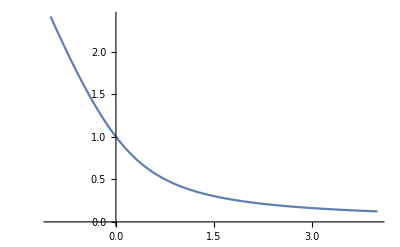

```mathematica
{{x->-1+a-√(-2 a+a^2)},{x->-1+a+√(-2 a+a^2)}}
Plot[xsym, {a, -1, 4}]
```

```mathematica
J11 =FullSimplify[ D[eq1, X[[1]]]/.X[[1]]->xsym/.X[[2]]->xsym/.X[[3]]->xsym/.X[[4]]->xsym/.X[[5]]->xsym/. X[[6]]->xsym]
J12 = FullSimplify[D[eq1,X[[2]]]/.X[[1]]->xsym/.X[[2]]->xsym/.X[[3]]->xsym/.X[[4]]->xsym/.X[[5]]->xsym/. X[[6]]->xsym]
J12 = FullSimplify[D[eq1, X[[2]]]/.X[[1]]->x/.X[[2]]->x/.X[[3]]->x/.X[[4]]->x/.X[[5]]->x/. X[[6]]->x]
J13 =FullSimplify [D[eq1, X[[3]]]/.X[[1]]->xsym/.X[[2]]->xsym/.X[[3]]->xsym/.X[[4]]->xsym/.X[[5]]->xsym/. X[[6]]->xsym]
J14 =FullSimplify [D[eq1, X[[4]]]/.X[[1]]->xsym/.X[[2]]->xsym/.X[[3]]->xsym/.X[[4]]->xsym/.X[[5]]->xsym/. X[[6]]->xsym]
J15 =FullSimplify [D[eq1, X[[5]]]/.X[[1]]->xsym/.X[[2]]->xsym/.X[[3]]->xsym/.X[[4]]->xsym/.X[[5]]->xsym/. X[[6]]->xsym]
J16 = FullSimplify [D[eq1, X[[6]]]/.X[[1]]->xsym/.X[[2]]->xsym/.X[[3]]->xsym/.X[[4]]->xsym/.X[[5]]->xsym/. X[[6]]->xsym]
```

-1

-a/((1-a+√(1+a^2))^2)

-a/(1+x)^2

0

0

0

-a/((1-a+√(1+a^2))^2)

```mathematica
-a/((1-a+√(1+a^2))^2)/.a->1
```

-1/2

```mathematica
J = {{-1, J12,0,0,  0, J12}, {J12, -1, J12, 0, 0, 0}, {0, J12, -1, J12, 0, 0}, {0,0, J12, -1, J12, 0},  {0, 0,0, J12, -1, J12},{J12,0, 0,0, J12, -1}};
eig1 = N[FullSimplify[Eigenvalues[J][[4]]]]/.x->xsym
```

-1.+a/((1.-a+√(1+a^2))^2)

```mathematica
acrit = NSolve[eig1==0, a][[1]][[1]][[2]]
```

1.64039

```mathematica
neq1 = eq1/.a->acrit;
neq2 = eq2/.a->acrit;
neq3 = eq3/.a->acrit;
neq4 = eq4/.a->acrit;
neq5 = eq5/.a-> acrit;
neq6 = eq6/.a->acrit;
```

```mathematica
NSolve[{neq1==0,neq2==0,neq3==0,neq4==0, neq5==0, neq6==0}, X]
```

{{x_1→-11.7657+0.812567 ⅈ,x_2→-2.23315+0.00863433 ⅈ,x_3→7.15478-0.821881 ⅈ,x_4→-0.848492+0.0114354 ⅈ,x_5→0.330176+0.00931369 ⅈ,x_6→-1.19913-0.0200697 ⅈ},{x_1→-0.720342+0.000660222 ⅈ,x_2→0.632459+0.00455263 ⅈ,x_3→-1.55558-0.00346257 ⅈ,x_4→-6.86566+0.0138478 ⅈ,x_5→-2.00485+0.00280234 ⅈ,x_6→1.95243-0.0184004 ⅈ},{x_1→-2.00645-0.068697 ⅈ,x_2→1.87754+0.437297 ⅈ,x_3→-0.71713-0.0159801 ⅈ,x_4→0.62232-0.110734 ⅈ,x_5→-1.5572+0.0846771 ⅈ,x_6→-6.78063-0.326563 ⅈ},{x_1→1.25721-0.154149 ⅈ,x_2→-0.698622+0.00281537 ⅈ,x_3→0.9045+0.103307 ⅈ,x_4→-1.72336-0.0493995 ⅈ,x_5→-6.44249+0.0508419 ⅈ,x_6→-1.8588+0.0465841 ⅈ},{x_1→-1.89671+0.120126 ⅈ,x_2→-6.37589+0.197362 ⅈ,x_3→-1.68879-0.131314 ⅈ,x_4→0.797084+0.240743 ⅈ,x_5→-0.695273+0.0111873 ⅈ,x_6→1.29803-0.438104 ⅈ},{x_1→-1.86181-0.394397 ⅈ,x_2→-5.50731-0.135827 ⅈ,x_3→-1.78258+0.405354 ⅈ,x_4→0.573816-0.720238 ⅈ,x_5→-0.636391-0.0109573 ⅈ,x_6→0.652719+0.856065 ⅈ},{x_1→0.490489+0.754989 ⅈ,x_2→-1.78299-0.457388 ⅈ,x_3→-5.33328+0.157474 ⅈ,x_4→-1.87585+0.443649 ⅈ,x_5→0.562016-0.912463 ⅈ,x_6→-0.621944+0.0137388 ⅈ},{x_1→-4.16569+1.95325 ⅈ,x_2→-1.23289-0.641358 ⅈ,x_3→0.064367+0.306474 ⅈ,x_4→-0.624699+0.231564 ⅈ,x_5→-0.179457-2.25973 ⅈ,x_6→-2.42319+0.409794 ⅈ},{x_1→-0.106044-0.546938 ⅈ,x_2→-1.47832+0.969249 ⅈ,x_3→-3.84637-0.814039 ⅈ,x_4→-2.33519-0.816891 ⅈ,x_5→-0.328358+1.36098 ⅈ,x_6→-0.467265-0.152358 ⅈ},{x_1→-0.437823-0.0485043 ⅈ,x_2→-0.15956-0.766856 ⅈ,x_3→-1.77787+1.02033 ⅈ,x_4→-3.89636-0.249896 ⅈ,x_5→-2.06508-0.971828 ⅈ,x_6→-0.224856+1.01675 ⅈ},{x_1→-0.433548-0.00465292 ⅈ,x_2→-0.195661+0.896308 ⅈ,x_3→-1.93748-1.00911 ⅈ,x_4→-3.89571-0.0237858 ⅈ,x_5→-1.90974+1.01377 ⅈ,x_6→-0.18941-0.872522 ⅈ},{x_1→-3.56155,x_2→-3.56155,x_3→-3.56155,x_4→-3.56155,x_5→-3.56155,x_6→-3.56155},{x_1→-1.88831-2.65077 ⅈ,x_2→-0.745336+0.495961 ⅈ,x_3→-0.0484989+0.0333733 ⅈ,x_4→-0.813558-0.556355 ⅈ,x_5→-2.34397+2.6174 ⅈ,x_6→-2.72188+0.0603939 ⅈ},{x_1→0.280777+1.84087×10^-7 ⅈ,x_2→0.280776-1.82396×10^-7 ⅈ,x_3→0.280776-1.69078×10^-9 ⅈ,x_4→0.280777+1.84087×10^-7 ⅈ,x_5→0.280776-1.82396×10^-7 ⅈ,x_6→0.280776-1.69078×10^-9 ⅈ},{x_1→0.280777+2.08177×10^-7 ⅈ,x_2→0.280777-2.6682×10^-7 ⅈ,x_3→0.280776+5.86427×10^-8 ⅈ,x_4→0.280777+2.08177×10^-7 ⅈ,x_5→0.280777-2.6682×10^-7 ⅈ,x_6→0.280776+5.86427×10^-8 ⅈ},{x_1→0.280776-1.53603×10^-7 ⅈ,x_2→0.280776+1.50579×10^-7 ⅈ,x_3→0.280777+3.02425×10^-9 ⅈ,x_4→0.280776-1.53603×10^-7 ⅈ,x_5→0.280776+1.50579×10^-7 ⅈ,x_6→0.280777+3.02425×10^-9 ⅈ},{x_1→0.280776-1.84356×10^-7 ⅈ,x_2→0.280776+2.36215×10^-7 ⅈ,x_3→0.280777-5.18594×10^-8 ⅈ,x_4→0.280776-1.84356×10^-7 ⅈ,x_5→0.280776+2.36215×10^-7 ⅈ,x_6→0.280777-5.18594×10^-8 ⅈ}}

```mathematica
eq1
```

1-x_1-(a x_2)/(1+x_2)-(a x_6)/(1+x_6)

```mathematica
neq1 = eq1/.a->(acrit+0.1)
neq2 = eq2/.a->(acrit+0.1);
neq3 = eq3/.a->(acrit+0.1);
neq4 = eq4/.a->(acrit+0.1);
neq5 = eq5/.a-> (acrit+0.1);
neq6 = eq6/.a-> (acrit+0.1 );
NSolve[{neq1==0,neq2==0,neq3==0,neq4==0, neq5==0, neq6==0}, X]
```

1-x_1-(1.74039 x_2)/(1+x_2)-(1.74039 x_6)/(1+x_6)

{{x_1→-11.6433+0.706848 ⅈ,x_2→-2.42621+0.00873819 ⅈ,x_3→6.94228-0.714324 ⅈ,x_4→-0.837198+0.010812 ⅈ,x_5→0.220246+0.0074763 ⅈ,x_6→-1.21737-0.0195502 ⅈ},{x_1→-0.707941-0.000335773 ⅈ,x_2→0.453373-0.00152642 ⅈ,x_3→-1.57536+0.00159344 ⅈ,x_4→-6.95902-0.00685093 ⅈ,x_5→-2.19748-0.00125767 ⅈ,x_6→2.02487+0.00837736 ⅈ},{x_1→-2.16351-0.084641 ⅈ,x_2→1.72383+0.451071 ⅈ,x_3→-0.695374-0.0183459 ⅈ,x_4→0.487936-0.108242 ⅈ,x_5→-1.62189+0.102987 ⅈ,x_6→-6.69254-0.342829 ⅈ},{x_1→-2.03739+0.0967475 ⅈ,x_2→-6.36996+0.152222 ⅈ,x_3→-1.76722-0.105927 ⅈ,x_4→0.663197+0.155111 ⅈ,x_5→-0.676163+0.00917976 ⅈ,x_6→1.22599-0.307332 ⅈ},{x_1→1.16185-0.162471 ⅈ,x_2→-0.675965+0.0039711 ⅈ,x_3→0.72755+0.0966591 ⅈ,x_4→-1.80052-0.0601625 ⅈ,x_5→-6.37018+0.0658123 ⅈ,x_6→-2.00429+0.0561914 ⅈ},{x_1→-1.94424-0.401688 ⅈ,x_2→-5.63514-0.0442674 ⅈ,x_3→-1.91198+0.405273 ⅈ,x_4→0.560712-0.663937 ⅈ,x_5→-0.624557-0.00358563 ⅈ,x_6→0.593653+0.708205 ⅈ},{x_1→0.390874+0.686438 ⅈ,x_2→-1.87374-0.513434 ⅈ,x_3→-5.35227+0.183614 ⅈ,x_4→-2.00621+0.496594 ⅈ,x_5→0.480617-0.870052 ⅈ,x_6→-0.60083+0.0168402 ⅈ},{x_1→-4.34456+2.16603 ⅈ,x_2→-1.22591-0.640293 ⅈ,x_3→0.0109333+0.251177 ⅈ,x_4→-0.633397+0.237422 ⅈ,x_5→-0.14715-2.41721 ⅈ,x_6→-2.62147+0.402871 ⅈ},{x_1→-0.428633-0.0342486 ⅈ,x_2→-0.202298-0.757546 ⅈ,x_3→-1.90497+1.12367 ⅈ,x_4→-4.0351-0.181929 ⅈ,x_5→-2.14717-1.08942 ⅈ,x_6→-0.243373+0.939475 ⅈ},{x_1→-0.168925-0.501381 ⅈ,x_2→-1.49697+1.08231 ⅈ,x_3→-3.92165-0.826648 ⅈ,x_4→-2.53534-0.926257 ⅈ,x_5→-0.390198+1.32803 ⅈ,x_6→-0.448466-0.15605 ⅈ},{x_1→-0.416558-0.00980758 ⅈ,x_2→-0.255677+0.863365 ⅈ,x_3→-2.0673-1.14655 ⅈ,x_4→-3.98212-0.050129 ⅈ,x_5→-1.99692+1.15636 ⅈ,x_6→-0.242976-0.813236 ⅈ},{x_1→-1.68897-2.78433 ⅈ,x_2→-0.713146+0.460272 ⅈ,x_3→-0.0945079+0.0609199 ⅈ,x_4→-0.854255-0.589001 ⅈ,x_5→-2.6973+2.72341 ⅈ,x_6→-2.91338+0.128729 ⅈ},{x_1→-3.74761,x_2→-3.74761,x_3→-3.74761,x_4→-3.74761,x_5→-3.74761,x_6→-3.74761},{x_1→0.175321,x_2→0.480776,x_3→0.175321,x_4→0.175321,x_5→0.480776,x_6→0.175321},{x_1→0.480776,x_2→0.175321,x_3→0.175321,x_4→0.480776,x_5→0.175321,x_6→0.175321},{x_1→0.175321,x_2→0.175321,x_3→0.480776,x_4→0.175321,x_5→0.175321,x_6→0.480776},{x_1→0.266837,x_2→0.266837,x_3→0.266837,x_4→0.266837,x_5→0.266837,x_6→0.266837}}

### Eigenvalues of a circulant matrix

```mathematica
Clear[n];
Clear[j];
eigj = -1 + a*(Exp[2*Pi*ⅈ*j/n] + Exp[2*Pi*(n-1)*j*ⅈ/n])
N[Exp[2*Pi*ⅈ*j/n] + Exp[2*Pi*(n-1)*j*ⅈ/n]/.n->6/.j->1]
```

-1+a (ⅇ^((2 ⅈ j π)/n)+ⅇ^((2 ⅈ j (-1+n) π)/n))

1.+0. ⅈ

```mathematica
Simplify[ComplexExpand[TrigExpand[ExpToTrig[eigj]]]]
```

(Cos[j π]+ⅈ Sin[j π]) (-Cos[j π]+2 a Cos[(j (-2+n) π)/n]+ⅈ Sin[j π])

```mathematica
xstar =-a+√(1+a^2);
α = a/(1+xstar)^2;
eigj =FullSimplify[-1 + 2*α*Cos[2*Pi*j/n]]
acrit = FullSimplify[Solve[eigj == 0, a, Reals, Assumptions->n∈Integers&& j∈Integers && j<n&&j>-1&&n>0]]
```

-1+(2 a Cos[(2 j π)/n])/((1-a+√(1+a^2))^2)

{{a→ConditionalExpression[1/4 (2+Cos[(2 j π)/n]+Sec[(2 j π)/n]+√(-10+4 Cos[(2 j π)/n]+Cos[(2 j π)/n]^2+4 Sec[(2 j π)/n]+Sec[(2 j π)/n]^2)), ]}}

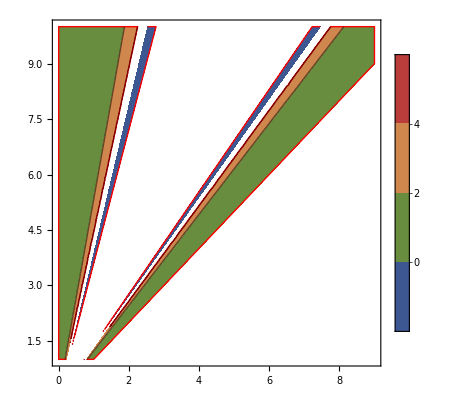

```mathematica
ContourPlot[acrit⟦1⟧⟦1⟧⟦2⟧⟦1⟧,{j, 0,9},{n,1,10},RegionFunction->Function[{j,n, z}, n>j],PlotLegends->Automatic, ColorFunction->"DarkRainbow", BoundaryStyle->Red]
```

Infinity::indet: Indeterminate expression -10+ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

ListContourPlot::invregion: {Function[{n,j,z},n>j],Function[{n,j,z},Im[z]=0]} must be a Boolean function.

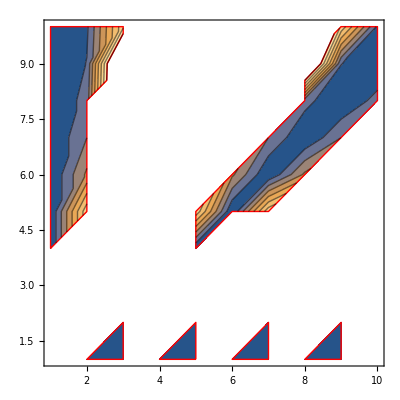

```mathematica
ListContourPlot[Table[acrit⟦1⟧⟦1⟧⟦2⟧⟦1⟧,{n,1,10,1},{j,0,9,1}], RegionFunction->{Function[{n, j, z}, n>j], Function[{n, j, z},Im[z]=0]}, BoundaryStyle->Red]
```

```mathematica
Table[acrit⟦1⟧⟦1⟧⟦2⟧⟦1⟧,{n,1,10,1},{j,0,9,1}]
```

Infinity::indet: Indeterminate expression -10+ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{{1,1,1,1,1,1,1,1,1,1},{1,ⅈ,1,ⅈ,1,ⅈ,1,ⅈ,1,ⅈ},{1,1/4 (-1/2+(3 ⅈ √7)/2),1/4 (-1/2+(3 ⅈ √7)/2),1,1/4 (-1/2+(3 ⅈ √7)/2),1/4 (-1/2+(3 ⅈ √7)/2),1,1/4 (-1/2+(3 ⅈ √7)/2),1/4 (-1/2+(3 ⅈ √7)/2),1},{1,Indeterminate,ⅈ,Indeterminate,1,Indeterminate,ⅈ,Indeterminate,1,Indeterminate},{1,1/4 (3+√5+1/4 (-1+√5)+√(-11+√5+1/16 (-1+√5)^2+4 (1+√5)+(1+√5)^2)),1/4 (3-√5+1/4 (-1-√5)+√(-11-√5+1/16 (-1-√5)^2+4 (1-√5)+(1-√5)^2)),1/4 (3-√5+1/4 (-1-√5)+√(-11-√5+1/16 (-1-√5)^2+4 (1-√5)+(1-√5)^2)),1/4 (3+√5+1/4 (-1+√5)+√(-11+√5+1/16 (-1+√5)^2+4 (1+√5)+(1+√5)^2)),1,1/4 (3+√5+1/4 (-1+√5)+√(-11+√5+1/16 (-1+√5)^2+4 (1+√5)+(1+√5)^2)),1/4 (3-√5+1/4 (-1-√5)+√(-11-√5+1/16 (-1-√5)^2+4 (1-√5)+(1-√5)^2)),1/4 (3-√5+1/4 (-1-√5)+√(-11-√5+1/16 (-1-√5)^2+4 (1-√5)+(1-√5)^2)),1/4 (3+√5+1/4 (-1+√5)+√(-11+√5+1/16 (-1+√5)^2+4 (1+√5)+(1+√5)^2))},{1,1/4 (9/2+(√17)/2),1/4 (-1/2+(3 ⅈ √7)/2),ⅈ,1/4 (-1/2+(3 ⅈ √7)/2),1/4 (9/2+(√17)/2),1,1/4 (9/2+(√17)/2),1/4 (-1/2+(3 ⅈ √7)/2),ⅈ},{1,1/4 (2+Csc[(3 π)/14]+Sin[(3 π)/14]+√(-10+4 Csc[(3 π)/14]+Csc[(3 π)/14]^2+4 Sin[(3 π)/14]+Sin[(3 π)/14]^2)),1/4 (2-Csc[π/14]-Sin[π/14]+√(-10-4 Csc[π/14]+Csc[π/14]^2-4 Sin[π/14]+Sin[π/14]^2)),1/4 (2-Cos[π/7]-Sec[π/7]+√(-10-4 Cos[π/7]+Cos[π/7]^2-4 Sec[π/7]+Sec[π/7]^2)),1/4 (2-Cos[π/7]-Sec[π/7]+√(-10-4 Cos[π/7]+Cos[π/7]^2-4 Sec[π/7]+Sec[π/7]^2)),1/4 (2-Csc[π/14]-Sin[π/14]+√(-10-4 Csc[π/14]+Csc[π/14]^2-4 Sin[π/14]+Sin[π/14]^2)),1/4 (2+Csc[(3 π)/14]+Sin[(3 π)/14]+√(-10+4 Csc[(3 π)/14]+Csc[(3 π)/14]^2+4 Sin[(3 π)/14]+Sin[(3 π)/14]^2)),1,1/4 (2+Csc[(3 π)/14]+Sin[(3 π)/14]+√(-10+4 Csc[(3 π)/14]+Csc[(3 π)/14]^2+4 Sin[(3 π)/14]+Sin[(3 π)/14]^2)),1/4 (2-Csc[π/14]-Sin[π/14]+√(-10-4 Csc[π/14]+Csc[π/14]^2-4 Sin[π/14]+Sin[π/14]^2))},{1,1/4 (2+1/(√2)+√2+√(-15/2+6 √2)),Indeterminate,1/4 (2-1/(√2)-√2+ⅈ √(15/2+6 √2)),ⅈ,1/4 (2-1/(√2)-√2+ⅈ √(15/2+6 √2)),Indeterminate,1/4 (2+1/(√2)+√2+√(-15/2+6 √2)),1,1/4 (2+1/(√2)+√2+√(-15/2+6 √2))},{1,1/4 (2+Cos[(2 π)/9]+Sec[(2 π)/9]+√(-10+4 Cos[(2 π)/9]+Cos[(2 π)/9]^2+4 Sec[(2 π)/9]+Sec[(2 π)/9]^2)),1/4 (2+Csc[π/18]+Sin[π/18]+√(-10+4 Csc[π/18]+Csc[π/18]^2+4 Sin[π/18]+Sin[π/18]^2)),1/4 (-1/2+(3 ⅈ √7)/2),1/4 (2-Cos[π/9]-Sec[π/9]+√(-10-4 Cos[π/9]+Cos[π/9]^2-4 Sec[π/9]+Sec[π/9]^2)),1/4 (2-Cos[π/9]-Sec[π/9]+√(-10-4 Cos[π/9]+Cos[π/9]^2-4 Sec[π/9]+Sec[π/9]^2)),1/4 (-1/2+(3 ⅈ √7)/2),1/4 (2+Csc[π/18]+Sin[π/18]+√(-10+4 Csc[π/18]+Csc[π/18]^2+4 Sin[π/18]+Sin[π/18]^2)),1/4 (2+Cos[(2 π)/9]+Sec[(2 π)/9]+√(-10+4 Cos[(2 π)/9]+Cos[(2 π)/9]^2+4 Sec[(2 π)/9]+Sec[(2 π)/9]^2)),1},{1,1/4 (1+√5+1/4 (1+√5)+√(-9+√5+4 (-1+√5)+(-1+√5)^2+1/16 (1+√5)^2)),1/4 (3+√5+1/4 (-1+√5)+√(-11+√5+1/16 (-1+√5)^2+4 (1+√5)+(1+√5)^2)),1/4 (1-√5+1/4 (1-√5)+√(-9-√5+4 (-1-√5)+(-1-√5)^2+1/16 (1-√5)^2)),1/4 (3-√5+1/4 (-1-√5)+√(-11-√5+1/16 (-1-√5)^2+4 (1-√5)+(1-√5)^2)),ⅈ,1/4 (3-√5+1/4 (-1-√5)+√(-11-√5+1/16 (-1-√5)^2+4 (1-√5)+(1-√5)^2)),1/4 (1-√5+1/4 (1-√5)+√(-9-√5+4 (-1-√5)+(-1-√5)^2+1/16 (1-√5)^2)),1/4 (3+√5+1/4 (-1+√5)+√(-11+√5+1/16 (-1+√5)^2+4 (1+√5)+(1+√5)^2)),1/4 (1+√5+1/4 (1+√5)+√(-9+√5+4 (-1+√5)+(-1+√5)^2+1/16 (1+√5)^2))}}

### Full analitical calculation

```mathematica
symeq =FullSimplify[ 1/2*(-nb*a + Sqrt[(nb*a)^2 + 4])/.nb->4]
```

-2 a+√(1+4 a^2)

```mathematica
alpha = FullSimplify[D[eq1, X[[2]]]/.X[[2]]-> symeq]
```

-(4 a)/((2-a nb+√(4+a^2 nb^2))^2)

```mathematica
FullSimplify[alpha/.nb->2]
```

-a/((1-a+√(1+a^2))^2)

```mathematica
Clear[n]
FullSimplify[Solve[1-xs-(n-1)*a*xs/(1+xs)==0, xs]]
```

{{xs→1/2 (a-a n-√(4+(a-a n)^2))},{xs→1/2 (a-a n+√(4+(a-a n)^2))}}

```mathematica
fun[A_, x_, i_, n_] := 1- x[[i]]-Sum[A[[i,j]]*x[[j]]/(1+x[[j]]), {j, DeleteCases[Range[1,n],i]}];
```

```mathematica
n=5;
A = {{b, a, a, a,a}, {a, b, a, a, a}, {a, a, b, a, a}, {a, a, a, b, a}, {a, a, a, a, b}};
```

```mathematica
X =Array[Subscript[x,#1]&,n] ;  
R = 1;
eq1 = fun[A, X, 1, n]/.X[[1]]->xs/.X[[2]]->xs/.X[[3]]->xs/.X[[4]]->xs/.X[[5]]->xs
```

1-xs-(4 a xs)/(1+xs)

```mathematica
FullSimplify[Solve[eq1==0, xs]]
```

{}

```mathematica
FullSimplify[-D[eq1, X[[2]]]-1]
```

-1+a/(1+x_2)^2

```mathematica
-a/(1+Subscript[x, 2])
```

```mathematica
Eigenvalues[A]
```

{-a+b,-a+b,-a+b,-a+b,4 a+b}

```mathematica
Clear[n]
xsym = 1/2 (a-a n+√(4+(a-a n)^2))
```

1/2 (a-a n+√(4+(a-a n)^2))

```mathematica
lambda = -1+a/(1+x)^2
```

-1+a/(1+x)^2

```mathematica
Solve[lambda==0, x]
```

{{x→-1-√a},{x→-1+√a}}

```mathematica
eq1 = x-Sqrt[a] + 1/.x->xsym
```

1-√a+1/2 (a-a n+√(4+(a-a n)^2))

```mathematica
InputForm[FullSimplify[Solve[eq1==0, a]][[2]][[1]][[2]]]
```

Solve::nongen: Solutions may not be valid for all values of parameters.

(n^2 + Sqrt[(-2 + n)^2*(-4 + n*(4 + n))])/(2*(-1 + n)^2)

1/2 (a-a n+√(4+(a-a n)^2))

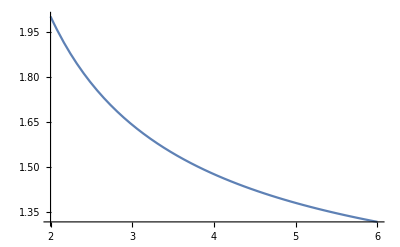

```mathematica
Plot[{(n^2+√((-2+n)^2 (-4+n (4+n))))/(2 (-1+n)^2)}, {n, 2, 6}]
```